## Hyperboloidal conformal Penrose diagrams

## Alex Vañó-Viñuales, October 2023.

## Supplementary material for article 2311.XXXXX (“Conformal diagrams for stationary and dynamical strong-field hyperboloidal slices”).

### MaTeX installation - execute only if MaTeX not installed

```mathematica
ResourceFunction["MaTeXInstall"]
```

Paclet[MaTeX,1.7.6,<>]

## Set location of repository (data in compressed files needs to be unzipped)

```mathematica
repolocation="~/other_repos/paper_repos/";
```

## Setup, basic conformal diagrams and data loader

## Setup

### Loading MaTeX and its preamble for his notebook

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathrsfs}\\DeclareSymbolFontAlphabet{\\mathrsfs}{rsfs}
\\newcommand{\\scri}{\\mathrsfs{I}}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{mathrsfs}\DeclareSymbolFontAlphabet{\mathrsfs}{rsfs}
\newcommand{\scri}{\mathrsfs{I}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
MaTeX["\\scri^+"]
```

-Graphics-

### Various formulas

#### Initialization

```mathematica
omega={Derivative[3][Ω][r]->0,Ω''[r]->-1/(aa rscri),Ω'[r]->-r/(aa rscri),Ω[r]->(-r^2+rscri^2)/(2 aa rscri)}/.r[]->r/.rscri[]->rscri/.aa->-3/Kcmc;
```

```mathematica
$Assumptions={rscri∈Reals,rscri>0,r∈Reals,r>0,1≥rscri,rscri≥r,Ω[r]∈Reals,Ω[r]≥0,Ω'[r]∈Reals,Ω'[r]≤0,aconf[r]∈Reals,aconf[r]≥0,mass∈Reals,mass≥0,Subscript[K, CMC]∈Reals,Subscript[K, CMC]≤0,Subscript[C, CMC]∈Reals,Subscript[C, CMC]≥0,Q∈Reals,Q≥0,mass≥Q,rp∈Reals,rp>0,α[r]∈Reals,α[r]>0,αb[r]∈Reals,αb[r]>0};
```

#### Physical domain quantities

```mathematica
(*to calculate the source functions*)
(*flat*)
(*Aexpr[r_]=(1-(2 mass)/r+Q^2/r^2)/.Q->0/.mass->0
hpexpr[r_]=(-Subscript[C, CMC]/r^2-(Subscript[K, CMC] r)/3)/(Aexpr[r]*√(Aexpr[r]+(-Subscript[C, CMC]/r^2-(Subscript[K, CMC] r)/3)^2))(*/.r->r[]*)/.Q->0/.mass->0/.Ccmc->0//Simplify*)
(*CMC trumpet*)
Aexprt[r_]=(1-(2 mass)/r+Q^2/r^2)/.Q->0
hpexprt[r_]=(-Subscript[C, CMC]/r^2-(Subscript[K, CMC] r)/3)/(Aexprt[r]*√(Aexprt[r]+(-Subscript[C, CMC]/r^2-(Subscript[K, CMC] r)/3)^2))(*/.r->r[]*)/.Q->0//Simplify
```

1-(2 mass)/r

(-Ccmc/r^2-(Kcmc r)/3)/((1-(2 mass)/r) √(1-(2 mass)/r+(Ccmc/r^2+(Kcmc r)/3)^2))

```mathematica
(*uncompactified*)
(*flat*)
(*flatunco=allvalg[{grrb[r[]]->(1-(Aexpr[r[]] hpexpr[r[]])^2)/Aexpr[r[]],gθθb[r[]]->1,χb[r[]]->1,βrb[r[]]->-Aexpr[r[]]^2hpexpr[r[]]/(1-(Aexpr[r[]] hpexpr[r[]])^2),αb[r[]]->Sqrt[Aexpr[r[]]/(1-(Aexpr[r[]] hpexpr[r[]])^2)]}]/.r[]->r//Simplify//Expand;*)
(*CMC*)
trumpetunco=allvalg[{grrb[r[]]->(1-(Aexprt[r[]] hpexprt[r[]])^2)/Aexprt[r[]],gθθb[r[]]->1,χb[r[]]->1,βrb[r[]]->-Aexprt[r[]]^2 hpexprt[r[]]/(1-(Aexprt[r[]] hpexprt[r[]])^2),αb[r[]]->Sqrt[Aexprt[r[]]/(1-(Aexprt[r[]] hpexprt[r[]])^2)]}]/.r[]->rp//Simplify//Expand;
```

#### Compactified domain quantities

```mathematica
(*compactified*)
(*flatsubsb={grrb''[r]->0,gθθb''[r]->0,χb''[r]->0,αb''[r]->(3 (Subscript[K, CMC]^2 Ω[r]^2+Subscript[K, CMC]^2 r^2 Ω'[r]^2+9 Ω[r]^3 Ω''[r]+Subscript[K, CMC]^2 r Ω[r] (-2 Ω'[r]+r Ω''[r])))/((Subscript[K, CMC]^2 r^2+9 Ω[r]^2)^(3/2)),βrb''[r]->0,grrb'[r]->0,gθθb'[r]->0,χb'[r]->0,αb'[r]->(Subscript[K, CMC]^2 r+9 Ω[r] Ω'[r])/(3 √(Subscript[K, CMC]^2 r^2+9 Ω[r]^2)),βrb'[r]->Subscript[K, CMC]/3,grrb[r]->1,gθθb[r]->1,χb[r]->1,αb[r]->1/3 √(Subscript[K, CMC]^2 r^2+9 Ω[r]^2),βrb[r]->(Subscript[K, CMC] r)/3}/.r[]->r;*)
trumpetsubsb={grrb''[r]->0,gθθb''[r]->0,χb''[r]->1/(9 r^6 Ω[r]^4)2 (36 Subscript[C, CMC]^2 aconf[r]^6 Ω[r]^2+27 Q^2 aconf[r]^4 r^2 Ω[r]^2+15 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3 Ω[r]^2+Subscript[K, CMC]^2 r^6 Ω[r]^2+3 aconf[r] r^2 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r] (-3 Ω[r]+4 r Ω'[r])-9 aconf[r]^2 r^4 (-3 Ω[r]^2-3 r^2 Ω'[r]^2+r Ω[r] (4 Ω'[r]+r Ω''[r]))),αb''[r]->(648 Subscript[C, CMC]^4 aconf[r]^12 Ω[r]+810 Subscript[C, CMC]^2 Q^2 aconf[r]^10 r^2 Ω[r]+459 Subscript[C, CMC]^2 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^9 r^3 Ω[r]+15 Subscript[K, CMC]^2 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^9 Ω[r]+2 Subscript[K, CMC]^4 r^12 Ω[r]+3 Subscript[K, CMC]^2 aconf[r] r^8 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) (-Ω[r]+2 r Ω'[r])-27 aconf[r]^7 r^2 ((-5 Subscript[C, CMC] Subscript[K, CMC] Q^2 r^3+15 m Q^2 r^3-2 Subscript[C, CMC]^2 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)) Ω[r]+4 Subscript[C, CMC]^2 r √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω'[r])+9 Subscript[K, CMC]^2 aconf[r]^2 r^10 (2 Ω[r]+r^2 Ω''[r])+81 aconf[r]^8 r^4 (2 (4 Subscript[C, CMC]^2+Q^4) Ω[r]+Subscript[C, CMC]^2 r^2 Ω''[r])+27 aconf[r]^6 r^6 ((4 Subscript[C, CMC]^2 Subscript[K, CMC]^2-4 Subscript[C, CMC] Subscript[K, CMC] m+6 (m^2+Q^2)) Ω[r]+3 Q^2 r^2 Ω''[r])+9 aconf[r]^4 r^5 ((4 Subscript[K, CMC]^2 Q^2 r^3+Subscript[C, CMC] Subscript[K, CMC] √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)-3 m √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)) Ω[r]-2 (Subscript[C, CMC] Subscript[K, CMC]-3 m) r √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω'[r]+9 r^5 Ω''[r])+27 aconf[r]^5 r^4 ((Subscript[C, CMC] Subscript[K, CMC] r^3-3 m r^3+Q^2 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)) Ω[r]-2 Q^2 r √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω'[r]+2 Subscript[C, CMC] Subscript[K, CMC] r^5 Ω''[r]-6 m r^5 Ω''[r]))/(27 aconf[r]^3 r^8 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)),βrb''[r]->1/(3 r^8)Subscript[C, CMC] aconf[r] (45 Subscript[C, CMC]^2 aconf[r]^6+36 Q^2 aconf[r]^4 r^2+21 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+27 aconf[r]^2 r^4+2 Subscript[K, CMC]^2 r^6-3 aconf[r] r^2 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)),grrb'[r]->0,gθθb'[r]->0,χb'[r]->-1/(3 r^3 Ω[r]^3)2 aconf[r] (√(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r]+3 aconf[r] r^2 (-Ω[r]+r Ω'[r])),αb'[r]->(-18 Subscript[C, CMC]^2 aconf[r]^6 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r]+Subscript[K, CMC]^2 r^6 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r]+27 Subscript[C, CMC]^2 aconf[r]^7 r^3 Ω'[r]+27 Q^2 aconf[r]^5 r^5 Ω'[r]+3 Subscript[K, CMC]^2 aconf[r] r^9 Ω'[r]+3 aconf[r]^3 r^3 ((-Subscript[C, CMC] Subscript[K, CMC]+3 m) √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r]+9 r^4 Ω'[r])-9 aconf[r]^4 (Q^2 r^2 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r]-2 (Subscript[C, CMC] Subscript[K, CMC]-3 m) r^6 Ω'[r]))/(9 aconf[r]^2 r^5 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)),βrb'[r]->1/(3 r^5)(3 Subscript[C, CMC] aconf[r]^3 r^2+Subscript[K, CMC] r^5-3 Subscript[C, CMC] aconf[r]^2 √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)),grrb[r]->1,gθθb[r]->1,χb[r]->aconf[r]^2/Ω[r]^2,αb[r]->1/(3 aconf[r] r^2)√(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r],βrb[r]->(Subscript[C, CMC] aconf[r]^3)/r^2+(Subscript[K, CMC] r)/3}/.r[]->r;
```

```mathematica
trumpetaconfp={χ[r]->aconf[r]^2/Ω[r]^2,grr[r]->(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6),gθθ[r]->1,α[r]->1/(3 aconf[r] r^2)√(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6) Ω[r],βr[r]->-1/(9 r^4 (-aconf[r]+r aconf'[r]))(3 Subscript[C, CMC] aconf[r]^3+Subscript[K, CMC] r^3) √(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)}/.r[]->r;
```

#### Values of parameters - trumpets

```mathematica
allvalg[rule_]:=DeleteDuplicates@Flatten[{Map[Table[Table[(Flatten@D[First@rule[[count]],{List@@First@rule[[count]],#}])[[count2]]
->(Flatten@D[Last@rule[[count]],{List@@First@rule[[count]],#}])[[count2]],{count2,1,Length[List@@First@rule[[count]]]^#}],{count,1,Length@rule}]&,{2,1}],rule}]
```

```mathematica
Kcmcset=-10/10;massset=10/10;Qset=0;
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.allvalg[{Ω[r[]]->1,ψ[r[]]->1,aconf[r[]]->1}]/.r[]->r//Simplify;
Discriminant[r^4/%,r](*/Kcmc^2/.Kcmc->Kcmcset*)
Solve[0==%,Ccmc];
N[%/.Kcmc->Kcmcset/.mass->massset/.Q->Qset,{∞,40(*200*)}]//Chop;
Cases[Cases[%,{Ccmc->Except[_Complex]}],{Ccmc->Except[0]}]
Ccmcset=Last@Last@%[[(*2*)1]]
N[Solve[(1/%%%%%%/.Kcmc->Kcmcset/.Ccmc->Ccmcset/.mass->massset/.Q->Qset)==0,r,Assumptions->None],{∞,100}]//Chop;
Cases[%,{r->Except[_Complex]}]
inmstR=Last@Last@%[[1]]
```

-64/9 Ccmc^4 Kcmc^2 (16 Ccmc^2+9 Ccmc^4 Kcmc^4-36 Ccmc^3 Kcmc^3 mass+42 Ccmc^2 Kcmc^2 mass^2+36 Ccmc Kcmc mass^3+24 Ccmc^3 Kcmc^5 mass^3-27 mass^4-108 Ccmc^2 Kcmc^4 mass^4+162 Ccmc Kcmc^3 mass^5-81 Kcmc^2 mass^6)

{{Ccmc→3.114839973711186876968031808295289455628}}

3.114839973711186876968031808295289455628

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→1.905072674868123960948418393272203882541},{r→1.905072674868123960951428908873948138955}}

1.905072674868123960948418393272203882541

(9 r^4 (aconf[r]-r aconf'[r])^2)/(Kcmc^2 r^6+9 r^4 aconf[r]^2+6 (Ccmc Kcmc-3 mass) r^3 aconf[r]^3+9 Ccmc^2 aconf[r]^6)

(9 r^4 (aconf[r]-r aconf'[r])^2)/(r^6+9 r^4 aconf[r]^2-36.68903984226712126180819084977173673377 r^3 aconf[r]^3+87.32005255646196619330713431878941222133 aconf[r]^6)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::precw: The precision of the differential equation ({{aconf'[r]==(0.05555555555555555555555555555555555555556 (r^6+9. r^4 aconf[«1»]^2-36.68903984226712126180819084977173673377 r^3 aconf[«1»]^3+87.32005255646196619330713431878941222133 aconf[«1»]^6) ((18. r^5 aconf[r])/Plus[«4»]-(5.29594285926070776320427851125734502885×10^20 r^3)/(√Plus[«4»])))/r^6,aconf[1]==0},{},{},{},{}}) is less than WorkingPrecision (100.).

Power::infy: Infinite expression 1/0^6 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {r,aconf[r]} = {0,-2.014906560873432030795354186957411613855879834366524493049336405719207825959548969800479360217940871×10^-11}.

{{aconf→InterpolatingFunction[…]}}

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

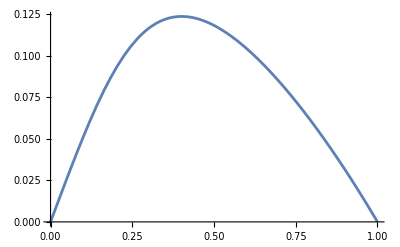

```mathematica
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.r[]->r//Simplify
%/.Kcmc->Kcmcset/.Ccmc->Ccmcset/.mass->massset/.Q->Qset//Simplify
(*NDSolve[{%==1,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->(*29*)15,PrecisionGoal->(*40*)20,WorkingPrecision->(*100*)50]*)
Solve[%==1,aconf'[r],Assumptions->None][[1,1]];
NDSolve[{First@%==Last@%,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->10(*29*),PrecisionGoal->15(*40*),WorkingPrecision->100]
lilu=%[[1,1,2]]
Plot[{lilu[r]},{r,0,1}]
```

InterpolatingFunction::dmval: Input value {1/100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/50000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3/100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.04286×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

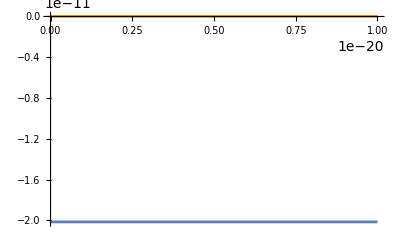

```mathematica
Prepend[Map[{#,lilu[#]}&,Range[1/100000,1,1/100000]],{0,0}];
lilulu=Interpolation[%];
Plot[{lilu[r],lilulu[r]},{r,0,0.00000000000000000001}]
```

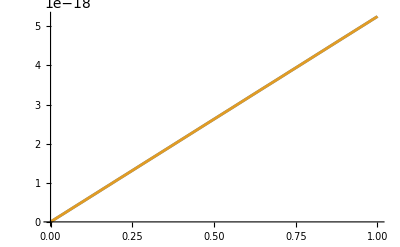

```mathematica
lilu=lilulu;
Plot[{lilulu[r],lilu[r]},{r,0,0.00000000000000001}]
```

#### Height function expression

```mathematica
hfuncdcomp=h'[r_]->FullSimplify[((-3 Subscript[C, CMC]-Subscript[K, CMC] rp^3)/(√(9+(9 Subscript[C, CMC]^2)/rp^4+(9 Q^2)/rp^2+(6 Subscript[C, CMC] Subscript[K, CMC])/rp-(18 m)/rp+Subscript[K, CMC]^2 rp^2) (Q^2+rp (-2 m+rp)))/.rp->r/aconf[r])(aconf[r]-r aconf'[r])/aconf[r]^2/.Q->0,Assumptions->{aconf[r]∈Reals,aconf[r]>0}]
```

h'[r_]→((Kcmc r^3+3 Ccmc aconf[r]^3) (-aconf[r]+r aconf'[r]))/(r aconf[r]^3 (r-2 mass aconf[r]) √(9+(Kcmc^2 r^2)/aconf[r]^2+(6 (Ccmc Kcmc-3 mass) aconf[r])/r+(9 Ccmc^2 aconf[r]^4)/r^4))

### Loader setup

```mathematica
searchDirectoryLevels=1;   (* how deep to search the directory tree *)
```

```mathematica
ReadPygraph[file_]:=Module[{command,times,timeSteps,data,spaceSteps},
command="grep Time " <>  file <> "| cut -d\"=\" -f2 > .readpygraph.tmp";
Run[command];
times=ReadList[".readpygraph.tmp",Number];
timeSteps=Length@times;
command="grep -v Time " <>  file <> "| cut -d\"=\" -f2 > .readpygraph.tmp";
Run[command];
data = ReadList[".readpygraph.tmp",{Number,Number}];
Print["read ",N[ByteCount@data/1024]," KByte of data;"];
DeleteFile[".readpygraph.tmp"];
spaceSteps= Length@data/timeSteps;
data = Partition[data,spaceSteps];
idata=data;
Table[{times[[i]],data[[i]]},{i,1,timeSteps}]
];
```

```mathematica
ReadPygraphLimitr[file_,n_]:=Module[{command,times,timeSteps,data,spaceSteps},
command="grep Time "<>file<>"| cut -d\"=\" -f2 > .readpygraph.tmp";Run[command];
times=ReadList[".readpygraph.tmp",Number];timeSteps=Length[times];
command="grep -v Time "<>file<>"| cut -d\"=\" -f2 > .readpygraph.tmp";Run[command];
data=ReadList[".readpygraph.tmp",{Number,Number}];Print["read ",N[ByteCount[data]/1024]," KByte of data;"];
DeleteFile[".readpygraph.tmp"];spaceSteps=Length[data]/timeSteps;data=Partition[data,spaceSteps];
data=Table[Table[data[[time,count]],{count,1,n}],{time,1,timeSteps}];idata=data;
Table[{times⟦i⟧,data⟦i⟧},{i,1,timeSteps}]]
```

```mathematica
ReadPygraphLimitt[file_,n_]:=Module[{command,times,timeSteps,data,spaceSteps},
command="grep Time " <>  file <> "| cut -d\"=\" -f2 > .readpygraph.tmp";Run[command];
times=ReadList[".readpygraph.tmp",Number];timeSteps=Length[times];
command="grep -v Time " <>  file <> "| cut -d\"=\" -f2 > .readpygraph.tmp";Run[command];
data = ReadList[".readpygraph.tmp",{Number,Number}];Print["read ",N[ByteCount@data/1024]," KByte of data;"];
DeleteFile[".readpygraph.tmp"];spaceSteps= Length@data/timeSteps;
data = Partition[data,spaceSteps];idata=data;
Table[{times[[i]],data[[i]]},{i,1,n}]
];
```

### Covers and lettering for Penrose diagrams

```mathematica
labe = 22;matexmagnification=2;
```

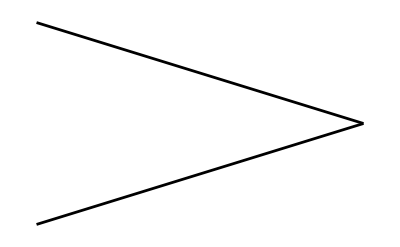
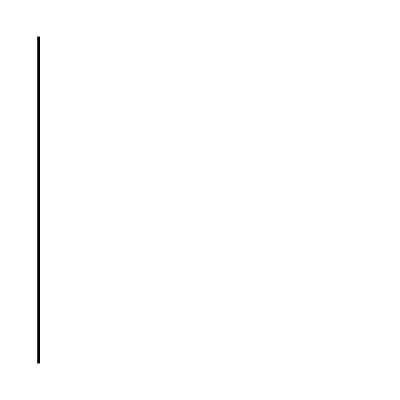

```mathematica
covermin = {Plot[{x - π/2, π/2 - x}, {x, 0, π/2}, 
   PlotRange -> {{0, π/2}, {-π/2, π/2}}, Ticks -> None, 
   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)], 
  ContourPlot[x == 0, {x, -0.01, π/2}, {y, -π/2, π/2}, Axes -> None, 
   Frame -> None, ContourStyle -> Black]}
```

```mathematica
(*lettersmin = Graphics[{Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(+\)\)]\)", {0 + 0.1, π/2 +  0.2}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(-\)\)]\)", {0 +  0.1, -π/2 - 0.2}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(0\)\)]\)", {π/2 + 0.2, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->2], {π/4 + 0.15, π/4 + 0.15}], 
   Text[MaTeX["\\scri^-",Magnification->2], {π/4 + 0.15, -π/4 - 0.15}]},  PlotRange -> {{0 - 0.3, π /2+ 0.3}, {-π/2 - 0.3, π/2 + 0.3}}]*)
lettersmin = Graphics[{Text[MaTeX["i^+",Magnification->matexmagnification], {0 + 0.1, π/2 +  0.16}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^-",Magnification->matexmagnification], {0 +  0.1, -π/2 - 0.2}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^0",Magnification->matexmagnification], {π/2 + 0.2, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {π/4 + 0.15, π/4 + 0.15}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {π/4 + 0.15, -π/4 - 0.15}]},  PlotRange -> {{0 - 0.3, π /2+ 0.3}, {-π/2 - 0.3, π/2 + 0.3}}]
```

-Graphics-

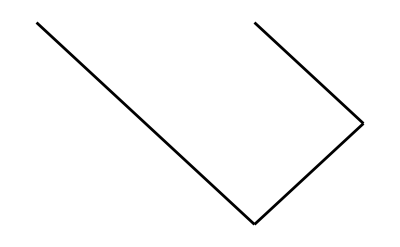
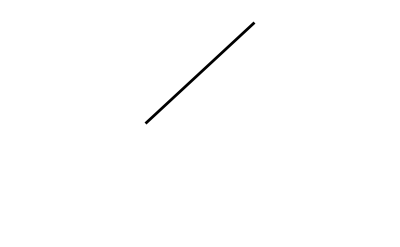
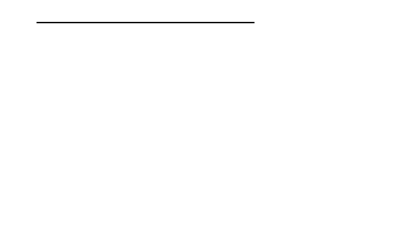

```mathematica
coverschw = {Plot[{x - π/2, π/2 - x,-x}, {x, -π/2, π/2},   PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None,   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)],
 Plot[{x}, {x, 0, π/2},  PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None,    PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)],
 Plot[{π/4}, {x,-π/4, π/4},  PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None,    PlotStyle ->{ Thick,Black}, Axes -> None(*,AspectRatio->1*)] }
```

```mathematica
(*lettersschw = Graphics[{Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(+\)\)]\)", {π/4 + 0.1, π/8 +  0.45}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(-\)\)]\)", {π/4 +  0.1, -π /8- 0.45}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(0\)\)]\)", {π /2+ 0.1, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {3π/8 + 0.1, π/8 + 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {3π/8 + 0.1, -π/8 - 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}],Text[MaTeX["\\tilde r=0",Magnification->1.8],{0,π/4+0.06}, BaseStyle -> {FontSize -> labe-2,FontFamily->Times}]},  PlotRange -> {{-π/4 - 0.01, π/2 + 0.25}, {-π/4 -0.13, π/4 + 0.14}}]*)
lettersschw = Graphics[{Text[MaTeX["i^+",Magnification->matexmagnification], {π/4 + 0.1, π/8 +  0.42}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^-",Magnification->matexmagnification], {π/4 +  0.1, -π /8- 0.45}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^0",Magnification->matexmagnification], {π /2+ 0.1, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {3π/8 + 0.1, π/8 + 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {3π/8 + 0.1, -π/8 - 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}],Text[MaTeX["\\tilde r=0",Magnification->1.8],{0,π/4+0.06}, BaseStyle -> {FontSize -> labe-2,FontFamily->Times}]},  PlotRange -> {{-π/4 - 0.01, π/2 + 0.25}, {-π/4 -0.13, π/4 + 0.14}}]
```

-Graphics-

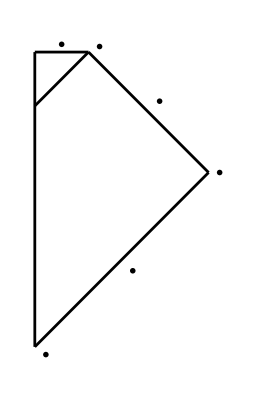
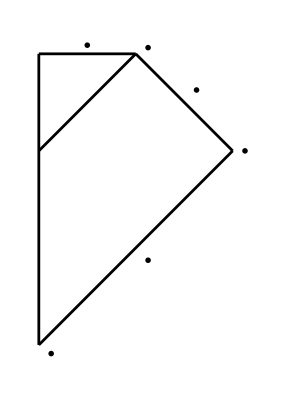
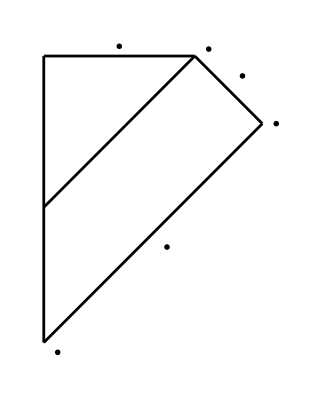

```mathematica
covercol[colpoint_] := {Plot[{x - π/2, π/2 - x}, {x, 0, π/2}, 
   PlotRange -> {{- (π/2-colpoint)/2, π/2+0.01}, {-π/2,colpoint/2+π/4}}, Ticks -> None, 
   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)],
 Plot[{colpoint+x,colpoint/2+π/4}, {x,  0,(π/2-colpoint)/2}, 
   PlotRange -> {{- (π/2-colpoint)/2, (π/2-colpoint)/2}, {colpoint,colpoint/2+π/4}}, Ticks -> None, 
   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)],
  ContourPlot[{x == 0(*,x==(π/2-colpoint)/2*)}, {x, -0.01, π/2}, {y, -π/2,colpoint/2+π/4}, Axes -> None, 
   Frame -> None, ContourStyle -> Black]};
(*letterscol[colpoint_]:= Graphics[{Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(+\)\)]\)", {(π/2-colpoint)/2+ 0.1, colpoint/2+π/4+  0.07}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(-\)\)]\)", {0+  0.1, -π /2- 0.07}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text["\!\(\*SuperscriptBox[\(i\), \(\(\\\ \)\(0\)\)]\)", {π /2+ 0.1, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {((π/2-colpoint)/2+π/2)/2+ 0.1,( colpoint/2+π/4)/2+ 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {π/4 + 0.1, -π/4 - 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}],Text[MaTeX["\\tilde r=0",Magnification->1.8],{(*0*)(π/2-colpoint)/4,colpoint/2+π/4+0.07}, BaseStyle -> {FontSize -> labe-2,FontFamily->Times}]},  PlotRange -> {{(*- (π/2-colpoint)/2 - 0.01*)-0.1, π/2 + 0.25}, {-π/2 -0.15,colpoint/2+π/4+ 0.14}}];*)
letterscol[colpoint_]:= Graphics[{Text[MaTeX["i^+",Magnification->matexmagnification], {(π/2-colpoint)/2+ 0.1, colpoint/2+π/4+ (* 0.07*)0.05}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^-",Magnification->matexmagnification], {0+  0.1, -π /2- 0.07}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^0",Magnification->matexmagnification], {π /2+ 0.1, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {((π/2-colpoint)/2+π/2)/2+ 0.1,( colpoint/2+π/4)/2+ 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {π/4 + 0.1, -π/4 - 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}],Text[MaTeX["\\tilde r=0",Magnification->1.8],{(*0*)(π/2-colpoint)/4,colpoint/2+π/4+0.07}, BaseStyle -> {FontSize -> labe-2,FontFamily->Times}]},  PlotRange -> {{(*- (π/2-colpoint)/2 - 0.01*)-0.1, π/2 + 0.25}, {-π/2 -0.15,colpoint/2+π/4+ 0.14}}];
{Show[letterscol[0.6],covercol[0.6]],Show[letterscol[0],covercol[0]],Show[letterscol[-0.6],covercol[-0.6]]}
```

```mathematica
makePlotLegend[names_, markers_, origin_, markerSize_, fontSize_, font_] := 
  Join @@ Table[{Text[Style[names[[i]], FontSize -> fontSize, FontFamily->font], 
      Offset[{1.5*markerSize, -(i - 0.5)*Max[markerSize, fontSize]*1.25}, 
       Scaled[origin]], {-1, 0}], 
     Inset[Show[markers[[i]], ImageSize -> markerSize], 
      Offset[{markerSize/2, -(i - 0.5)*Max[markerSize, fontSize]*1.25}, 
       Scaled[origin]], {0, 0}, 
      Background -> Directive[Opacity[0], White]]}, {i, 1, 
     Length[names]}];(*copied from \
http://stackoverflow.com/questions/3463437/plotting-legends-in-mathematica*)
```

## Basic construction of conformal Carter-Penrose diagrams

### Minkowski

#### Equations

```mathematica
uf = t - r; vf = t + r;
```

```mathematica
Uf = ArcTan[uf]; Vf = ArcTan[vf];
```

```mathematica
Tf = (Uf + Vf)/2; Rf =( Vf - Uf)/2;
```

```mathematica
listrf[rval_] := {Rf, Tf} /. {r -> rval}
listtf[tval_] := {Rf, Tf} /. {t -> tval}
```

```mathematica
listuf[uval_] := {ArcTan[vvf] - ArcTan[uuf],    ArcTan[uuf] + ArcTan[vvf]} /2/. {uuf -> uval}
listvf[vval_] := {ArcTan[vvf] - ArcTan[uuf],    ArcTan[uuf] + ArcTan[vvf]}/2 /. {vvf -> vval}
```

```mathematica
listttf[tval_] := {Rf, Tf} /. {t -> tval}
```

#### Graphs

```mathematica
listtime =   Map[listtf[#] &, {0, 0.3, 0.8, 1.6, 4, 15, -0.3, -0.8, -1.6, -4, -15}];
```

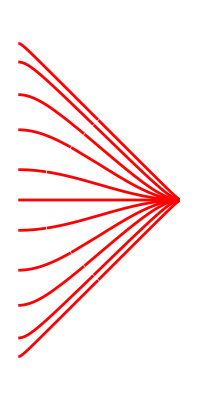

```mathematica
time = ParametricPlot[listtime, {r, 0, 50},   PlotRange -> {{0, π/2}, {-π/2, π/2}}, Ticks -> None, Axes -> None,   PlotStyle ->{{Red}},PlotPoints->200]
```

```mathematica
listradius = Map[listrf[#] &, {0, 0.3, 0.8, 1.6, 4, 15}];
```

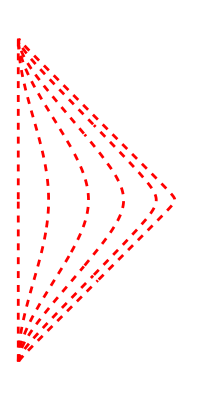

```mathematica
space = ParametricPlot[listradius, {t, -50, 50},   PlotRange -> {{0, π/2}, {-π/2, π/2}}, Ticks -> None, Axes -> None,   PlotStyle ->{{Red,Dashed}},PlotPoints->200]
```

```mathematica
Show[time,space,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},Epilog->makePlotLegend[(*{"r̃ = const","t̃ = const"}*){MaTeX["\\tilde r=\\textrm{const}",Magnification->1.7],MaTeX["\\tilde t=\\textrm{const}",Magnification->1.7]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[Red,Dashed],Red},{0.46,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-

```mathematica
listlightout=Map[listuf[#]&,{-2.5,-1.1,-0.5,-0.1,0.3,0.8,1.6,4}];
listlightin=Map[listvf[#]&,{-2.5,-1.1,-0.5,-0.1,0.3,0.8,1.6,4}];
```

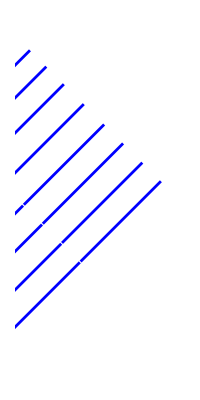

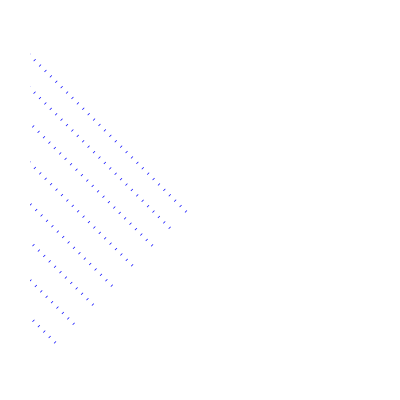

```mathematica
lightout=ParametricPlot[listlightout,{vvf,-50,50},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,Axes->None,PlotStyle->Blue,PlotPoints->200]
lightin=ParametricPlot[listlightin,{uuf,-50,50},PlotRange->{{0,π},{-π/2,π/2}},Ticks->None,Axes->None,PlotStyle->{{Blue,Dotted}},PlotPoints->200]
```

```mathematica
Show[lightin,lightout,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},Epilog->makePlotLegend[(*{"light in","light out"}*){MaTeX["\\textrm{light in}",Magnification->1.7],MaTeX["\\textrm{light out}",Magnification->1.7]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[Blue,Dotted],Blue},{0.46,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-

### Schwarzschild

#### Equations

```mathematica
(*Starting with Kruskal-Szekeres coordinates.*)
```

```mathematica
uso =Sqrt[r/(2mass)-1] Exp[r/(4mass)]Cosh[t/(4mass)]; vso =Sqrt[r/(2mass)-1] Exp[r/(4mass)]Sinh[t/(4mass)]; (*set -rhs for symmetric spacetime*)
usi =Sqrt[1-r/(2mass)] Exp[r/(4mass)]Sinh[t/(4mass)];vsi =Sqrt[1-r/(2mass)] Exp[r/(4mass)]Cosh[t/(4mass)];(*set -rhs for white hole*)
```

```mathematica
Uso = ArcTan[uso+vso]; Vso = ArcTan[uso-vso];
Usi = ArcTan[usi+vsi]; Vsi = ArcTan[usi-vsi];
```

```mathematica
Tso = (Uso - Vso)/2; Rso = (Uso+Vso)/2;
Tsi = (Usi - Vsi)/2; Rsi = (Usi+Vsi)/2;
```

```mathematica
listrso[rval_] := {Rso, Tso} /. {r -> rval}/.mass->massset
listtso[tval_] := {Rso, Tso} /. {t -> tval}/.mass->massset
listrsi[rval_] := {Rsi, Tsi} /. {r -> rval}/.mass->massset
listtsi[tval_] := {Rsi, Tsi} /. {t -> tval}/.mass->massset
```

#### Graphs

```mathematica
darkgreen=RGBColor[0,0.7,0.3];
```

```mathematica
listpruto=Map[listtso[#]&, {0,1.6, 4, 50, -1.6, -4, -50}];
listpruti=Map[listtsi[#] &, {0,1.6, 4,50, -1.6, -4, -50}];
```

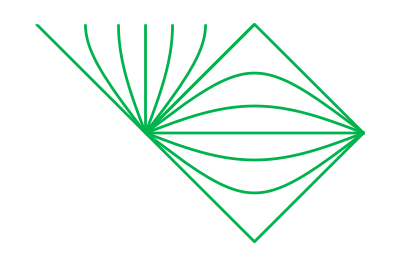

```mathematica
timeschw=Show[{ParametricPlot[listpruto, {r, 2, 100},   PlotRange -> {{-π/4,π/2}, {-π/4(*4*), π/4(*4*)}}, Ticks -> None, Axes -> None,   PlotStyle -> darkgreen],ParametricPlot[listpruti, {r,0,2},   PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,   PlotStyle -> darkgreen]}]
```

```mathematica
listpruro = Map[listrso[#] &, {2.001,2.05,2.2,2.5,3,4,6,80}];
listpruri = Map[listrsi[#] &, {0,1.4,1.8,1.95,1.999}];
```

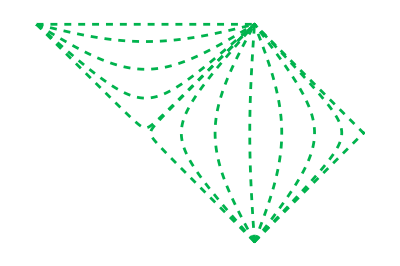

```mathematica
spaceschw = Show[{ParametricPlot[listpruro, {t, -100, 100},   PlotRange -> {{-π/4,π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,   PlotStyle ->Directive[ {darkgreen,Dashed}]],ParametricPlot[listpruri, {t, -100, 100},   PlotRange -> {{-π/4,π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,   PlotStyle -> Directive[ {darkgreen,Dashed}]]}]
```

```mathematica
Show[{lettersschw,timeschw,spaceschw,coverschw},Epilog->makePlotLegend[{MaTeX["\\tilde r=\\textrm{const}",Magnification->1.7],MaTeX["\\tilde t=\\textrm{const}",Magnification->1.7]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[darkgreen,Dashed],darkgreen},{0.16,0.28},labe-2,labe-2,"Times"],ImageSize->500]
```

-Graphics-

## Load code data

### Select code output data

```mathematica
runn="single";
conv=1;
```

```mathematica
tagcov="c4";
```

```mathematica
allDataFiles=FileNames["*yg",repolocation<>"HypPenroseDiagrams/data/"];
```

```mathematica
pretag="pentrevol_";(*for regular initial data of Minkowski perturbed by a scalar field*)
```

```mathematica
pretag="imitateoldoslong_";(*for trumpet relaxation*)
```

```mathematica
chif=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_chi"<>"*"<>tagcov<>"*"<>runn<>"*"]&]
grrf=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_grr"<>"*"<>tagcov<>"*"<>runn<>"*"]&]
alphaf=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_alpha"<>"*"<>tagcov<>"*"<>runn<>"*"]&]
betarf=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_betar"<>"*"<>tagcov<>"*"<>runn<>"*"]&]
Phif=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_phi"<>"*"<>tagcov<>"*"<>runn<>"*"]&]
Rf=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_R"<>"*"<>tagcov<>"*"<>runn<>"*"]&]
Tf=Select[allDataFiles,StringMatchQ[#,"*"<>pretag<>"*"<>"_T"<>"*"<>tagcov<>"*"<>runn<>"*"]&]

varfall={chif,grrf,alphaf,betarf,Phif,Rf,Tf};
```

{~/other_repos/paper_repos/HypPenroseDiagrams/data/imitateoldoslong_ev_chi_c4_single.yg}

{~/other_repos/paper_repos/HypPenroseDiagrams/data/imitateoldoslong_ev_grr_c4_single.yg}

{~/other_repos/paper_repos/HypPenroseDiagrams/data/imitateoldoslong_ev_alpha_c4_single.yg}

{~/other_repos/paper_repos/HypPenroseDiagrams/data/imitateoldoslong_ev_betar_c4_single.yg}

{}

{}

{}

```mathematica
varnall={"χ","γ_rr","α","β^r","Φ̄","R","T"}
```

{χ,γ_rr,α,β^r,Φ̄,R,T}

```mathematica
selectedvars={1,2,3,4};(*select here the variables to load*)
```

```mathematica
varf=Part[varfall,selectedvars];
varn=Part[varnall,selectedvars]
vmax=Length@selectedvars
```

{χ,γ_rr,α,β^r}

4

### Load data

```mathematica
vard=Table[Map[ReadPygraph[#]&,varf[[num]]],{num,1,vmax}];
```

read 2676.33 KByte of data;

read 2535.13 KByte of data;

read 2644.94 KByte of data;

read 2492.11 KByte of data;

```mathematica
times=vard[[;;,;;,;;,1]];
```

```mathematica
timeSteps=Table[Map[Length,times[[num]]],{num,1,vmax}]
```

{{51},{51},{51},{51}}

```mathematica
dt=Table[Map[#[[2]]-#[[1]]&,times[[num]]],{num,1,vmax}]
```

{{1.},{1.},{1.},{1.}}

```mathematica
dx=Table[Map[#[[1,2,2,1]]-#[[1,2,1,1]]&,vard[[num]]],{num,1,vmax}]
```

{{0.0049999999999999996704025},{0.0049999999999999996704025},{0.0049999999999999996704025},{0.0049999999999999996704025}}

## Stationary

## Minkowski (in terms of the compactified radial coordinate)

### Common definitions and expressions

```mathematica
minparsubs={aconf->Ω,Ccmc->0, mass->0,Kcmc->Kcmcset,rscri->1};
```

#### Equations

```mathematica
uf = t - r/Ω[r]/.omega/.minparsubs; vf = t + r/Ω[r]/.omega/.minparsubs;
```

```mathematica
Uf = ArcTan[uf]; Vf = ArcTan[vf];
```

```mathematica
Tf = (Uf + Vf)/2; Rf =( Vf - Uf)/2;
```

```mathematica
listrf[rval_] := {Rf, Tf} /. {r -> rval}
listtf[tval_] := {Rf, Tf} /. {t -> tval}
```

### CMC Minkowski slices from closed-form expressions

#### Assign data

```mathematica
(*Clear/@{χc,grrc,gθθc,αc,βrc,aconfc};*)
Clear@χc;Clear@grrc;Clear@gθθc;Clear@αc;Clear@βrc;Clear@aconfc;
```

```mathematica
χc[r_]=1;grrc[r_]=1;gθθc[r_]=1/Sqrt[grrc[r]];αc[r_]=αb[r]/.trumpetsubsb/.Ccmc->0/.Q->0/.mass->0/.aconf->Ω/.omega//Simplify;
βrc[r_]=βrb[r]/.trumpetsubsb/.Ccmc->0/.Q->0/.mass->0/.aconf->Ω/.omega//Simplify;
```

#### Height function

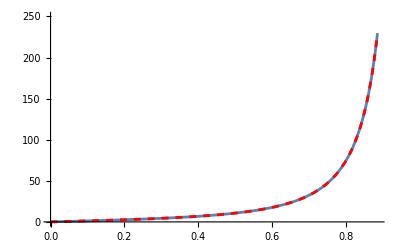

```mathematica
(*h'(r)*)
Last@hfuncdcomp/.minparsubs/.omega/.minparsubs//Evaluate;
Plot[%,{r,0,1}(*,PlotRange->{-20,5}*)]//Quiet;
hpnumcomp[r_]=(-βrc[r]grrc[r]/χc[r]/A)/.A->αc[r]^2-βrc[r]^2 grrc[r]/χc[r]/.minparsubs//Simplify;
Plot[%,{r,0,1},PlotStyle->{Red,Dashed}]//Quiet;
Show[%%%,%,PlotRange->{0,250}]//Quiet
```

```mathematica
NDSolve[{h'[r]==hpnumcomp[r],h[0]==0},h,{r,0,1}]
hfcompcmc=%[[1,1,2]];
```

NDSolve::ndsz: At r == 1., step size is effectively zero; singularity or stiff system suspected.

{{h→InterpolatingFunction[…]}}

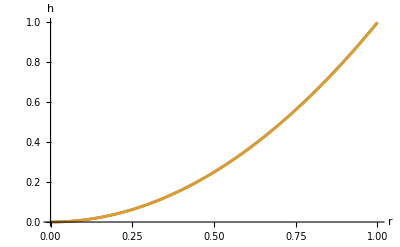

```mathematica
Plot[{hfcompcmc[r]Ω[r],(Sqrt[3^2/Kcmc^2+r^2/Ω[r]^2]+3/Kcmc)Ω[r]}/.omega/.minparsubs//Evaluate,{r,0,1},AxesLabel->{"r","h"}]//Quiet
```

#### Equations

```mathematica
thscmc = {t -> t +hfcompcmc[r]};
```

```mathematica
(*ths = {t -> t +hfnumcompresc[r]/Ω[r]/.omega/.minparsubs};*)
```

```mathematica
listttfcmc[tval_] := {Rf, Tf} /. thscmc/. {t -> tval}
```

#### Graphs

```mathematica
colourmink=RGBColor[0.7,0,0.8];
```

```mathematica
hlistcmc=Map[listttfcmc[#]&,{10,3.5,1.25,0.25,-0.5,-2,-5}];
```

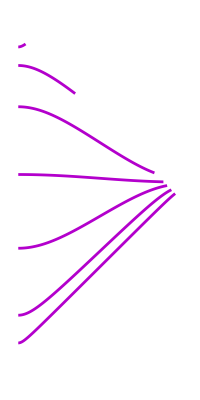

```mathematica
phlmink=ParametricPlot[hlistcmc,{r,0,0.99},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,PlotStyle->colourmink,BaseStyle->{FontSize->labe-2},Axes->None, PlotPoints->200]
```

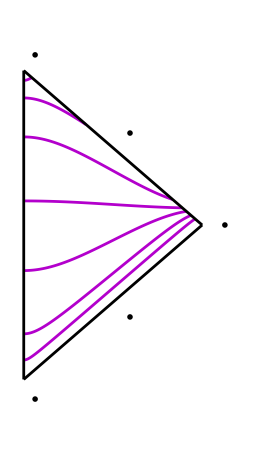

```mathematica
Show[phlmink,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},ImageSize->{260,450}]
```

### Scalar-field perturbed Minkowski slices from numerical data (requires having loaded data with pretag “pentrevol_”)

#### Assign data from code’s output

```mathematica
Clear@χc;Clear@grrc;Clear@gθθc;Clear@αc;Clear@βrc;Clear@aconfc;
```

```mathematica
tvalindex=1;(*use data at t=0, first time iteration*)
χc=Interpolation[vard[[1,1,tvalindex,2]]];
grrc=Interpolation[vard[[2,1,tvalindex,2]]];
gθθc=Interpolation[Map[{#[[1]],1/Sqrt[#[[2]]]}&,vard[[2,1,tvalindex,2]]]];
αc=Interpolation[vard[[3,1,tvalindex,2]]];
βrc=Interpolation[vard[[4,1,tvalindex,2]]];
(*compatification factor*)
aconfc[r_]=Sqrt[χc[r]/gθθc[r]]Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1//Simplify;
```

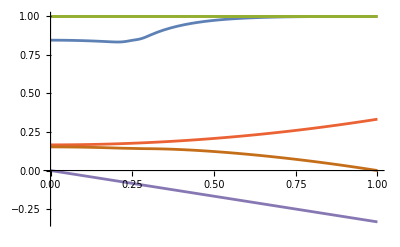

```mathematica
Plot[{χc[r],grrc[r],gθθc[r],αc[r],βrc[r],aconfc[r]},{r,0,1}]//Quiet
```

#### Height function

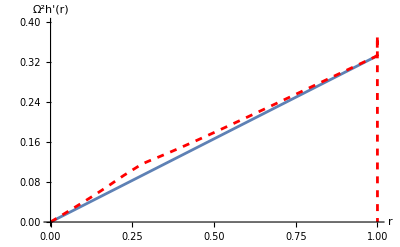

```mathematica
(*h'(r)*)
Last@hfuncdcomp/.minparsubs/.omega/.minparsubs//Evaluate;
Plot[(Ω[r]^2/.omega/.minparsubs)%,{r,0,1}(*,PlotRange->{-20,5}*)]//Quiet;
hpnumcomp[r_]=(-βrc[r]grrc[r]/χc[r]/A)/.A->αc[r]^2-βrc[r]^2 grrc[r]/χc[r]/.minparsubs//Simplify;
Plot[(Ω[r]^2/.omega/.minparsubs)%,{r,0,1},PlotStyle->{Red,Dashed}]//Quiet;
Show[%%%,%,PlotRange->{0,(*20*)0.4},AxesLabel->{"r","Ω^2h'(r)"}]//Quiet
```

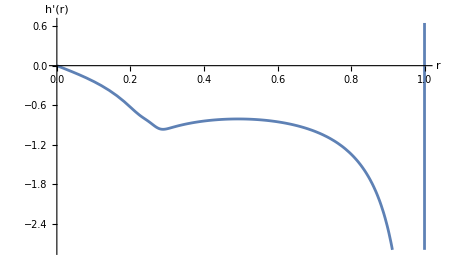
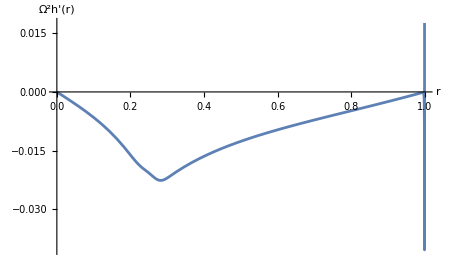

Difference in h' (or Ω^2h')due to the presence of the scalar field perturbation.

```mathematica
{Plot[(Last@hfuncdcomp/.minparsubs/.omega/.minparsubs)-hpnumcomp[r]//Evaluate,{r,0,1},AxesLabel->{"r","h'(r)"},ImageSize->450],Plot[(Ω[r]^2/.omega/.minparsubs)((Last@hfuncdcomp/.minparsubs/.omega/.minparsubs)-hpnumcomp[r])//Evaluate,{r,0,1},AxesLabel->{"r","Ω^2h'(r)"},ImageSize->450]}//Quiet
Style["Difference in h' (or Ω^2h')due to the presence of the scalar field perturbation.",Purple]
```

```mathematica
NDSolve[{h'[r]==hpnumcomp[r],h[0]==0},h,{r,0,1}]
hfnumcomp=%[[1,1,2]];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At r == 0.999885, step size is effectively zero; singularity or stiff system suspected.

{{h→InterpolatingFunction[…]}}

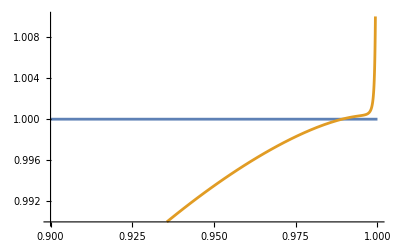

```mathematica
(*setting the integration constant for the height function so that they conincide with the Minkowski one asymptotically*)
hfcomp//Clear
hconst=-1.3;
Plot[{1,(hfnumcomp[r]+hconst)/(Sqrt[3^2/Kcmc^2+r^2/Ω[r]^2]+ 3/Kcmc)}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0.9,1},PlotRange->{0.99,1.01}]
hfcomp[r_]=hfnumcomp[r]+hconst;(*adding an integration constant to the numerical h so that it coincides (as much as possible) with the Minkowski case at infinity (where the height function diverges)*)
```

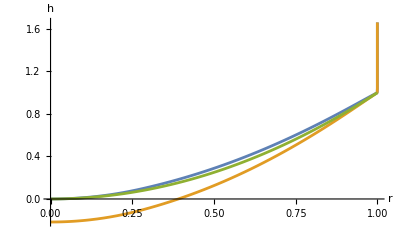

```mathematica
Plot[{(hfnumcomp[r])Ω[r],(hfcomp[r])Ω[r],(Sqrt[3^2/Kcmc^2+r^2/Ω[r]^2]+3/Kcmc)Ω[r]}/.omega/.minparsubs//Evaluate,{r,0,1},AxesLabel->{"r","h"}]//Quiet
```

#### Equations

```mathematica
ths = {t -> t +hfcomp[r]};
```

```mathematica
(*ths = {t -> t +hfnumcompresc[r]/Ω[r]/.omega/.minparsubs};*)
```

```mathematica
listttfpert[tval_] := {Rf, Tf} /. ths /. {t -> tval}
```

#### Graphs

```mathematica
colourpert=Black;
```

```mathematica
hlistpert=Map[listttfpert[#]&,{10,3.5,1.25,0.25,-0.5,-2,-5}];
```

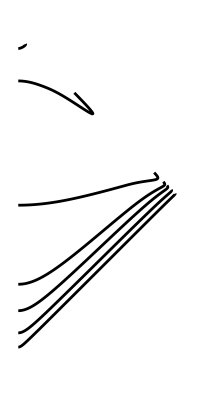

```mathematica
phlpert=ParametricPlot[hlistpert,{r,0,0.99},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,PlotStyle->colourpert,BaseStyle->{FontSize->labe-2(*16*)}(*,PlotLabel->"a = "<>ToString[aa]*),Axes->None, PlotPoints->200]
```

```mathematica
Show[phlmink,phlpert,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},Epilog->makePlotLegend[(*{"r̃ = const","t̃ = const"}*){MaTeX["\\textrm{CMC Minkowski}",Magnification->1.7],MaTeX["\\textrm{perturbed}",Magnification->1.7]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[colourmink],Directive[colourpert]},{0.21,0.18},labe-2,labe-2,"Times"],ImageSize->{260,450}]
```

-Graphics-

### Final

## Schwarzschild (including CMC and non-CMC stationary data)

### Select data: evaluate either “Closed form [...]” or “Numerical [...]” subsections and the rest

```mathematica
schwsubs={Q->0,omega,Ccmc->Ccmcset,mass->massset,Kcmc->Kcmcset,rscri->1,allvalg[{aconf[r]->lilu[r]}]}//Flatten;
```

#### Closed-form expressions for constant-mean-curvature (CMC) slices

```mathematica
Clear@χc;Clear@grrc;Clear@gθθc;Clear@αc;Clear@βrc;Clear@aconfc;
```

```mathematica
exprtag="closedform";
```

```mathematica
χc[r_]=χb[r]/.trumpetsubsb/.Q->0//Simplify;(*spatial conformal factor*)
grrc[r_]=1;(*rr component of conformal spatial metric*)
gθθc[r_]=1/Sqrt[grrc[r]];(*θθ component over r^2 of conformal spatial metric*)
αc[r_]=αb[r]/.trumpetsubsb/.Q->0//Simplify;(*lapse*)
βrc[r_]=βrb[r]/.trumpetsubsb/.Q->0//Simplify;(*shift*)
aconfc[r_]=Sqrt[χc[r]/gθθc[r]]Ω[r]//Evaluate;(*compatification factor*)
c=1;tvalindex=1;
```

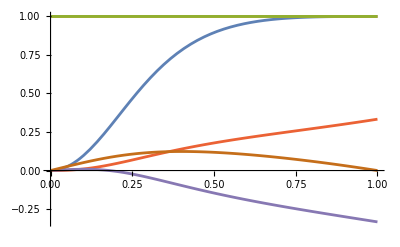

```mathematica
Plot[{χc[r],grrc[r],gθθc[r],αc[r],βrc[r],aconfc[r]}//.schwsubs//Evaluate,{r,0,1}]//Quiet
```

#### Numerical (requires having loaded data with pretag “imitateoldoslong_”)

```mathematica
Clear@χc;Clear@grrc;Clear@gθθc;Clear@αc;Clear@βrc;Clear@aconfc;
```

```mathematica
exprtag="numerical";
```

```mathematica
tvalindex=(*1*)timeSteps[[1,1]];(*the trumpet initial data is taken to be CMC Schwarzschild; if tval>1, it will no longer be CMC -- take the last available time (timeSteps[[1,1]]) to use non-CMC stationary data*)
χc=Interpolation[vard[[1,1,tvalindex,2]]];(*spatial conformal factor*)
grrc=Interpolation[vard[[2,1,tvalindex,2]]];(*rr component of conformal spatial metric*)
gθθc=Interpolation[Map[{#[[1]],1/Sqrt[#[[2]]]}&,vard[[2,1,tvalindex,2]]]];(*θθ component over r^2 of conformal spatial metric*)
αc=Interpolation[vard[[3,1,tvalindex,2]]];(*lapse*)
βrc=Interpolation[vard[[4,1,tvalindex,2]]];(*shift*)
aconfc[r_]=Sqrt[χc[r]/gθθc[r]]Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1//Simplify;(*compatification factor*)
```

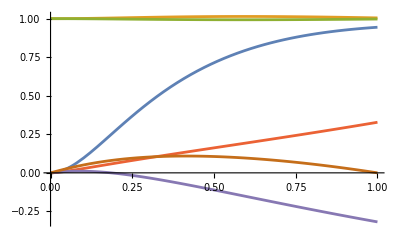

```mathematica
Plot[{χc[r],grrc[r],gθθc[r],αc[r],βrc[r],aconfc[r]},{r,0,1}]//Quiet
```

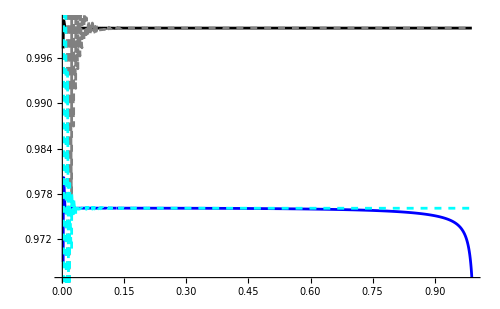

{{{1.},{0.976031}},{{1.},{0.976084}}}

Value of c taken to be c = 0.98797 -- It must be 1 if CMC data is being used.

```mathematica
(*in case the value of const=c^2 is needed and it is not 1*)(*imitateoldoslong_*)
{((α[r]^2-βr[r]^2 grr[r]/χ[r])/Ω[r]^2//Simplify)/(1-2mass Sqrt[χ[r]Sqrt[grr[r]]]Ω[r]/r)}/.omega/.Kcmc->Kcmcset/.rscri->1/.mass->massset;
Prepend[Table[%/.allvalg[{α[r]->αc[r],βr[r]->βrc[r],χ[r]->χc[r],grr[r]->grrc[r]}],{var,1,vard[[1]]//Length}],%/.allvalg[{α[r]->Interpolation[vard[[3,1,1,2]]][r],βr[r]->Interpolation[vard[[4,1,1,2]]][r],χ[r]->Interpolation[vard[[1,1,1,2]]][r],grr[r]->Interpolation[vard[[2,1,1,2]]][r]}]];
Plot[%,{r,0.002,0.99}(*,PlotRange->{0.99,1.04}*),PlotStyle->{Black,Blue},ImageSize->500]//Quiet;
{((grr[r]/χ[r]))/(1/α[r]^2*(Ω[r]^2/aconf[r]^2(aconf[r]-r*aconf'[r]))^2)}/.allvalg[{aconf[r]->Sqrt[χ[r]Sqrt[grr[r]]]Ω[r]}]/.omega/.Kcmc->Kcmcset/.rscri->1/.mass->massset;
Prepend[Table[%/.allvalg[{α[r]->αc[r],βr[r]->βrc[r],χ[r]->χc[r],grr[r]->grrc[r]}],{var,1,vard[[1]]//Length}],%/.allvalg[{α[r]->Interpolation[vard[[3,1,1,2]]][r],βr[r]->Interpolation[vard[[4,1,1,2]]][r],χ[r]->Interpolation[vard[[1,1,1,2]]][r],grr[r]->Interpolation[vard[[2,1,1,2]]][r]}]];
Plot[%,{r,0.002,0.99}(*,PlotRange->{0.99,1.04}*),PlotStyle->{{Gray,Dashed},{Cyan,Dashed}},ImageSize->500]//Quiet;
Show[%%%%,%]
{%%%%%%,%%%}/.r->0.5
const=%[[2,2,1]];c=Sqrt[const];
Style["Value of c taken to be c = "<>ToString[c]<>" -- It must be 1 if CMC data is being used.",Blue]
```

#### Evaluate

```mathematica
Which[exprtag=="closedform",subvals=schwsubs;,exprtag=="numerical",subvals={};,True,Clear@subvals]
```

```mathematica
FindRoot[(r/aconfc[r]//.subvals)==2massset,{r,0.1}];
rhornum=%[[1,2]](*location of the horizon in the compactified radial coordinate*)
```

0.130552

```mathematica
minkheight=(Sqrt[3^2/Kcmc^2+rphys^2]+ 3/Kcmc)/.Kcmc->Kcmcset;
```

#### Equations

```mathematica
(*Kruskal-Szekeres coordinates.*)
uso =Sqrt[rphys/(2mass)-1] Exp[rphys/(4mass)]Cosh[tphys/(4mass)]; vso =Sqrt[rphys/(2mass)-1] Exp[rphys/(4mass)]Sinh[tphys/(4mass)]; (*set -rhs for symmetric spacetime*)
usi =Sqrt[1-rphys/(2mass)] Exp[rphys/(4mass)]Sinh[tphys/(4mass)];vsi =Sqrt[1-rphys/(2mass)] Exp[rphys/(4mass)]Cosh[tphys/(4mass)];(*set -rhs for white hole*)
```

```mathematica
Uso = ArcTan[uso+vso]; Vso = ArcTan[uso-vso];
Usi = ArcTan[usi+vsi]; Vsi = ArcTan[usi-vsi];
```

```mathematica
Tso = (Uso - Vso)/2; Rso = (Uso+Vso)/2;
Tsi = (Usi - Vsi)/2; Rsi = (Usi+Vsi)/2;
```

```mathematica
Which[exprtag=="closedform",subaconf=aconf->lilu;,exprtag=="numerical",subaconf=aconf->aconfc;,True,Clear@subaconf;Print["Something went wrong -- possibly tag 'exprtag' not set."]]
```

```mathematica
listrso[rval_] = {Rso, Tso} /.mass->massset/.rphys->r/aconf[r]/.subaconf/. {r -> rval};
listtso[tval_] = {Rso, Tso} /. {tphys -> tval}/.mass->massset/.rphys->r/aconf[r]/.subaconf;
listrsi[rval_] = {Rsi, Tsi} /.mass->massset/.rphys->r/aconf[r]/.subaconf/. {r -> rval};
listtsi[tval_] = {Rsi, Tsi} /. {tphys -> tval}/.mass->massset/.rphys->r/aconf[r]/.subaconf;
```

#### Constant radius curves for diagrams and other bits (re-evaluate if the location of the trumpet changes or if a different colour is desired)

```mathematica
getclose=0.001;
listpruro = Map[listrso[#] &, {rhornum+getclose,0.15,0.22,0.3,0.4,0.6,0.94}];
listpruri = Map[listrsi[#] &, {0+getclose,0.01,0.05,0.1,rhornum-getclose}];
```

```mathematica
colourspatial=Orange;
```

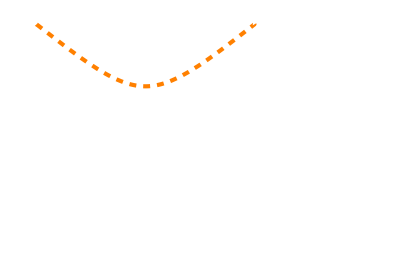

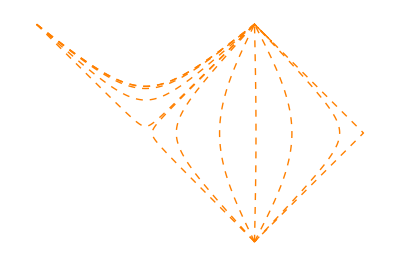

```mathematica
inrad=Show[ParametricPlot[listrsi[0+getclose],{tphys,-100,80},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->{colourspatial,Dashed,AbsoluteThickness[3]},Axes->None]]
spacebh = Show[{ParametricPlot[listpruro, {tphys, -100, 100},   PlotRange -> {{-π/4,π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,   PlotStyle ->  {{colourspatial,Dashed,AbsoluteThickness[1]}}],ParametricPlot[listpruri, {tphys,-100, 100},   PlotRange -> {{-π/4,π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,   PlotStyle -> {{colourspatial,Dashed,AbsoluteThickness[1]}}]}]
```

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

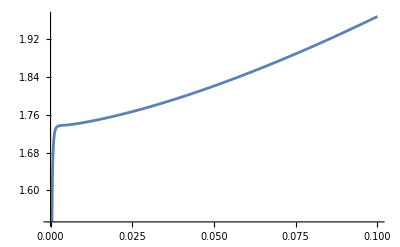

1.7436

-Graphics-

```mathematica
r/aconfc[r]//.subvals;
Plot[%,{r,0,0.1}]
inmstSchwrad=%%/.r->0.01
R0val= Graphics[Text[MaTeX["\\tilde r_{trum} ="<>ToString[NumberForm[inmstSchwrad,{3,2}]],Magnification->1.8],If[tvalindex>1,{0,π/4-0.09},{0,π/4-0.29}], BaseStyle -> {FontFamily->Times,FontSize -> labe-1,Black(*Blue*)}],  PlotRange -> {{-π/4 - 0.2, π/2 + 0.2}, {-π/4 -0.2, π/4 + 0.2}}]
(*If [radtag=="physical"||radtag=="phystort"||radtag=="physdeltah",R0val= Graphics[Text["(r̃)_trum = "<>ToString[NumberForm[rphystrum,{3,2}]],{0,π/4-0.29}, BaseStyle -> {FontFamily->Times,FontSize -> labe-1,Black(*Blue*)}],  PlotRange -> {{-π/4 - 0.2, π/2 + 0.2}, {-π/4 -0.2, π/4 + 0.2}}]]*)
```

### Construction using the physical radial coordinate (only for closed-form expressions)

#### Height function

```mathematica
exprtag="closedform";
```

```mathematica
{χc[r],grrc[r],gθθc[r],αc[r],βrc[r]}/.allvalg[{aconf[r]->1}]/.allvalg[{Ω[r]->1}]
```

{1,1,1,(√(9 Ccmc^2+6 (Ccmc Kcmc-3 mass) r^3+9 r^4+Kcmc^2 r^6))/(3 r^2),Ccmc/r^2+(Kcmc r)/3}

```mathematica
(*grphysrphysc[rphys_]=χb[r]/αb[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2/.trumpetsubsb/.aconf->Function[{r},1]/.Q->0/.r->rphys*)(*same as below, but using exclusively closed-form expression*)
grphysrphysc[rphys_]=χc[r]/αc[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2/.aconf->Function[{r},1]/.Q->0/.r->rphys
%-grrb[rp]/.trumpetunco/.rp->rphys//Simplify(*check*)
```

(9 rphys^4)/(9 Ccmc^2+6 (Ccmc Kcmc-3 mass) rphys^3+9 rphys^4+Kcmc^2 rphys^6)

0

```mathematica
(*βrphysc[rphys_]=(Simplify[-Sqrt[(αb[r]^2-Ω[r]^2(1-2mass aconf[r]/r+Q^2 aconf[r]^2/r^2))χb[r]/grrb[r]]/.grrb[r]->χb[r]/αb[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2,Assumptions->{(aconf[r]-r aconf'[r])∈Reals,(aconf[r]-r aconf'[r])>0,Ω[r]∈Reals,Ω[r]>0,aconf[r]∈Reals,aconf[r]>0,αb[r]∈Reals,αb[r]>0,Kcmc r^3+3 Ccmc aconf[r]^3∈Reals,Kcmc r^3+3 Ccmc aconf[r]^3<0}]/.trumpetsubsb//Simplify)/.Abs[Kcmc r^3+3 Ccmc aconf[r]^3]->-(Kcmc r^3+3 Ccmc aconf[r]^3)/.aconf->Function[{r},1]/.Q->0/.r->rphys//Simplify*)(*same as below, but using exclusively closed-form expression*)
βrphysc[rphys_]=Simplify[Simplify[-Sqrt[(αc[r]^2-Ω[r]^2(1-2mass aconf[r]/r+Q^2 aconf[r]^2/r^2))χc[r]/grr[r]]/.grr[r]->χc[r]/αc[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2,Assumptions->{(aconf[r]-r aconf'[r])∈Reals,(aconf[r]-r aconf'[r])>0,Ω[r]∈Reals,Ω[r]>0,aconf[r]∈Reals,aconf[r]>0,αb[r]∈Reals,αb[r]>0,Kcmc r^3+3 Ccmc aconf[r]^3∈Reals,Kcmc r^3+3 Ccmc aconf[r]^3<0}]/.aconf->Function[{r},1]/.Q->0/.r->rphys,Assumptions->{(3 Ccmc+Kcmc rphys^3)∈Reals,(3 Ccmc+Kcmc rphys^3)<0}]
%-βrb[rp]/.trumpetunco/.rp->rphys//Simplify(*check*)
```

((3 Ccmc+Kcmc rphys^3) √(9 Ccmc^2+6 Ccmc Kcmc rphys^3+rphys^3 (-18 mass+9 rphys+Kcmc^2 rphys^3)))/(9 rphys^4)

0

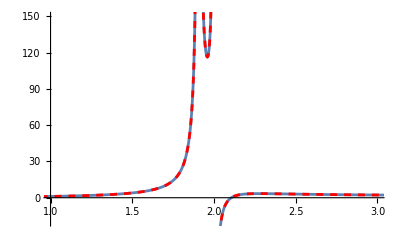

```mathematica
(*h'(rphys)*)
Last@hfuncdcomp/.Ccmc->Ccmcset/.mass->massset/.Kcmc->Kcmcset/.allvalg[{aconf[r]->1}]//Evaluate;
Plot[%,{r,0,10},PlotRange->All]//Quiet;
hppcomp[r_]=((-βrphysc[r]grphysrphysc[r]/χc[r]/A)/.A->αc[r]^2-βrphysc[r]^2 grphysrphysc[r]/χc[r]//Simplify)/.allvalg[{aconf[r]->1}]/.allvalg[{Ω[r]->1}]//.subvals//Evaluate;
Plot[%,{r,0,10},PlotStyle->{Red,Dashed},PlotRange->All]//Quiet;
Show[%%%,%,PlotRange->{{1,3},{-20,150}},AxesOrigin->{1,0}]//Quiet
```

```mathematica
rphyshornum=2massset;(*location of the horizon*)
rphystrum=inmstR;(*location of the trumpet*)
rphysmax=100000;(*maximum value of the radius up to which the integration is performed*)
```

NDSolve::ndsz: At r == 2., step size is effectively zero; singularity or stiff system suspected.

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {1.90507} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{hfu→InterpolatingFunction[…]}}

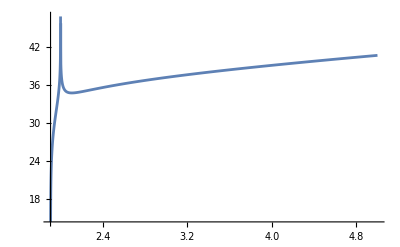

Piecewise[{{InterpolatingFunction[…][r], r<2}, {InterpolatingFunction[…][r], r>2}, {0, True}}]

InterpolatingFunction::dmval: Input value {1.90514} lies outside the range of data in the interpolating function. Extrapolation will be used.

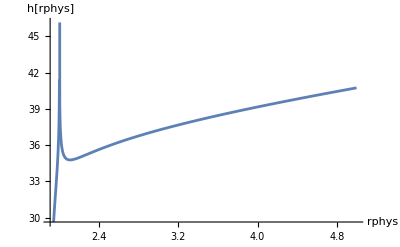

```mathematica
hppcomp[r];
NDSolve[{%==hfu'[r],hfu[rphyshornum-0.002]==40},hfu,{r,rphystrum+0.0002,rphysmax}]
Plot[%[[1,1,2]][r],{r,rphystrum,rphyshornum}];
NDSolve[{%%%==hfu'[r],hfu[rphyshornum+0.002]==40},hfu,{r,rphyshornum+0.002,rphysmax}]
Plot[%[[1,1,2]][r],{r,rphyshornum,5}];
Show[{%%%,%},PlotRange->{{rphystrum,5},Automatic}]
hpnumcomp[r_]=Piecewise[{{%%%%%[[1,1,2]][r],r<rphyshornum},{%%%[[1,1,2]][r],r>rphyshornum}}]
Plot[hpnumcomp[rphys],{rphys,rphystrum,5},AxesLabel->{"rphys", "h[rphys]"}]
```

```mathematica
(*setting the integration constant for the height function so that they conincide with the Minkowski one asymptotically*)
{hpnumcomp[r]+hc,minkheight/.rphys->r}/r/.r->rphysmax(*h/r is expected to be 1 asymptotically, comparing this*)
Solve[%[[1]]==%[[2]],hc]
hconstval=%[[1,1,2]];
```

{(100056.+hc)/100000,(-3+√10000000009)/100000}

{{hc→-58.6941}}

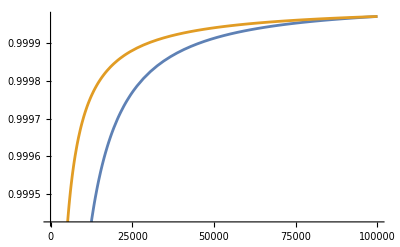

```mathematica
Clear@hpcomp
hconst=hconstval(*-59*);
Plot[{hpnumcomp[r]+hconst,minkheight/.rphys->r}/r//Evaluate,{r,rphystrum,100000},ImageSize->400]
hpcomp[r_]=hpnumcomp[r]+hconst;(*adding an integration constant to the numerical h so that it coincides (as much as possible) with the Minkowski case at infinity (where the height function diverges)*)
```

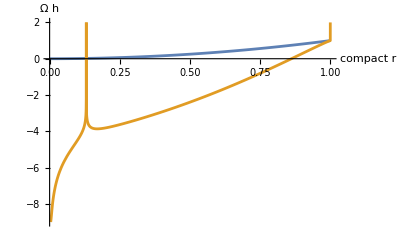

```mathematica
(*comparison between Ω rescaled Minkowski (blue) and Schwarzschild (yellow) height functions*)
Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys]/.rphys->r/lilu[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-9,2},AxesLabel->{"compact r", "Ω h"},ImageSize->400]//Quiet
```

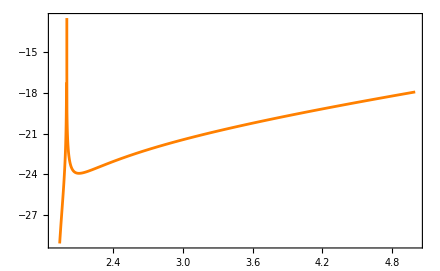

```mathematica
Plot[hpcomp[rphys],{rphys,rphystrum,5},Frame->True,FrameLabel->{MaTeX["\\tilde r",Magnification->1.4],MaTeX["h(\\tilde r)",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440,PlotStyle->Orange]//Quiet
```

InterpolatingFunction::dmval: Input value {1.90508} lies outside the range of data in the interpolating function. Extrapolation will be used.

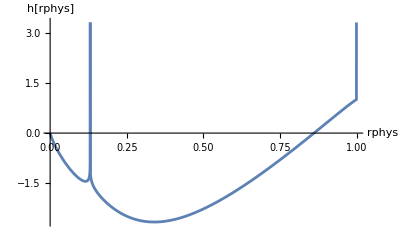

```mathematica
Plot[lilu[r]hpcomp[r/lilu[r]],{r,0,1},AxesLabel->{"rphys", "h[rphys]"}]
```

#### Equations

```mathematica
listttso[tval_]:= {Rso, Tso} /. {tphys -> tval+hpcomp[rphys]}/.mass->massset;
listttsi[tval_] := {Rsi, Tsi} /. {tphys -> tval+ hpcomp[rphys]}/.mass->massset;
```

#### Graphs

```mathematica
colourp=Orange;
```

```mathematica
listttt={-15,-24,-27.75,-30.25,-32.5,-36}+54
hlisto=Map[listttso[#]&,listttt];
hlisti=Map[listttsi[#]&,listttt];
```

{39,30,26.25,23.75,21.5,18}

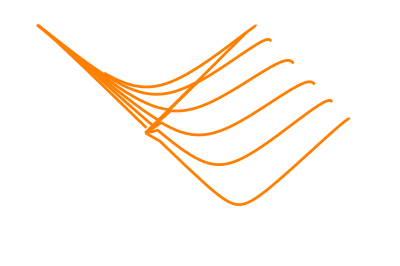

```mathematica
getclose=0.001;
hypfolp=Show[{ParametricPlot[hlisto,{rphys,rphyshornum,20},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourp,Axes->None],ParametricPlot[hlisti,{rphys,rphystrum+getclose,rphyshornum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourp,Axes->None]}]
```

```mathematica
Show[{lettersschw,spacebh,hypfolp,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourp,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

### Construction integrating for Δh = h - f in physical Kerr-Schild coordinates (only for closed-form expressions)

#### Height function

```mathematica
exprtag="closedform";
```

```mathematica
rphyshornum=2massset;(*location of the horizon*)
rphystrum=inmstR;(*location of the trumpet*)
rphysmax=100000;(*maximum value of the radius up to which the integration is performed*)
```

```mathematica
fks[rphys_]=Piecewise[{{-2massset Log[1-rphys/2/massset],rphys<rphyshornum},{- 2massset Log[rphys/2/massset-1],rphys>rphyshornum}}](*height function f(rphys) that includes the divergence at the horizon, used when transforming to Kerr-Schild coordinates*)
```

Piecewise[{{-2 Log[1-rphys/2], rphys<2}, {-2 Log[-1+rphys/2], rphys>2}, {0, True}}]

```mathematica
grphysrphysc[rphys_]=χc[r]/αc[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2/.aconf->Function[{r},1]/.Q->0/.r->rphys
```

(9 rphys^4)/(9 Ccmc^2+6 (Ccmc Kcmc-3 mass) rphys^3+9 rphys^4+Kcmc^2 rphys^6)

```mathematica
βrphysc[rphys_]=Simplify[Simplify[-Sqrt[(αc[r]^2-Ω[r]^2(1-2mass aconf[r]/r+Q^2 aconf[r]^2/r^2))χc[r]/grr[r]]/.grr[r]->χc[r]/αc[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2,Assumptions->{(aconf[r]-r aconf'[r])∈Reals,(aconf[r]-r aconf'[r])>0,Ω[r]∈Reals,Ω[r]>0,aconf[r]∈Reals,aconf[r]>0,αb[r]∈Reals,αb[r]>0,Kcmc r^3+3 Ccmc aconf[r]^3∈Reals,Kcmc r^3+3 Ccmc aconf[r]^3<0}]/.aconf->Function[{r},1]/.Q->0/.r->rphys,Assumptions->{(3 Ccmc+Kcmc rphys^3)∈Reals,(3 Ccmc+Kcmc rphys^3)<0}]
```

((3 Ccmc+Kcmc rphys^3) √(9 Ccmc^2+6 Ccmc Kcmc rphys^3+rphys^3 (-18 mass+9 rphys+Kcmc^2 rphys^3)))/(9 rphys^4)

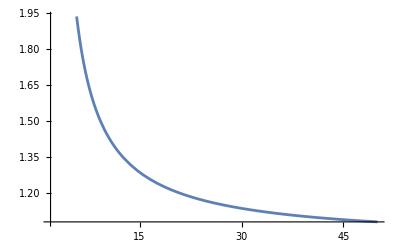

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction[…]

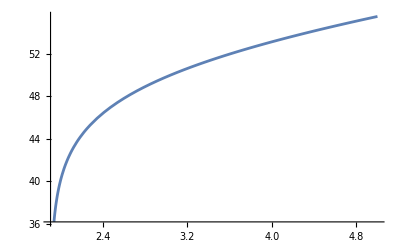

```mathematica
hppcomp[r_]=((-βrphysc[r]grphysrphysc[r]/χc[r]/A)/.A->αc[r]^2-βrphysc[r]^2 grphysrphysc[r]/χc[r]//Simplify)/.allvalg[{aconf[r]->1}]/.allvalg[{Ω[r]->1}]//.subvals//Evaluate;
hppcomp[r]-D[fks[r],r]//Simplify;
Plot[%,{r,inmstR,50}]
NDSolve[{%%==hfu'[r],hfu[rphyshornum-0.002]==40},hfu,{r,rphystrum+0.0002,rphysmax}]
dhpnumcomp=%[[1,1,2]]
Plot[dhpnumcomp[r],{r,rphystrum,5}]
```

```mathematica
(*setting the integration constant for the height function so that they conincide with the Minkowski one asymptotically*)
{dhpnumcomp[r]+fks[r]+hc,minkheight/.rphys->r}/r/.r->rphysmax(*h/r is expected to be 1 asymptotically, comparing this*)
Solve[%[[1]]==%[[2]],hc]
hconstval=%[[1,1,2]];
```

{(100070.+hc)/100000,(-3+√10000000009)/100000}

{{hc→-72.665}}

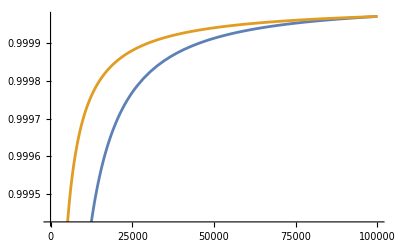

```mathematica
Clear@dhpcomp
hconst=hconstval;
Plot[{dhpnumcomp[r]+fks[r]+hconst,minkheight/.rphys->r}/r//Evaluate,{r,rphystrum,100000},ImageSize->400]
dhpcomp[r_]=dhpnumcomp[r]+hconst;(*adding an integration constant to the numerical h so that it coincides (as much as possible) with the Minkowski case at infinity (where the height function diverges)*)
```

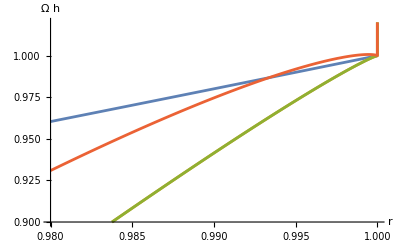
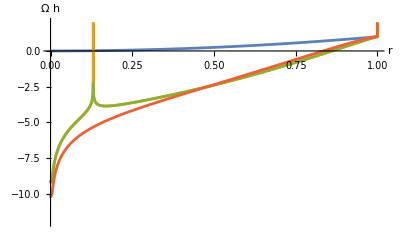

```mathematica
(*comparison between Ω rescaled Minkowski (blue) and Schwarzschild (yellow intefrating for h and green integrating for Δh) height functions and Δh in red*)
{Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys]/.rphys->r/lilu[r],dhpcomp[rphys]+fks[rphys]/.rphys->r/lilu[r],dhpcomp[rphys]/.rphys->r/lilu[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0.98,1},PlotRange->{0.9,1.02},AxesLabel->{"r", "Ω h"},ImageSize->400],Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys]/.rphys->r/lilu[r],dhpcomp[rphys]+fks[rphys]/.rphys->r/lilu[r],dhpcomp[rphys]/.rphys->r/lilu[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-12,2},AxesLabel->{"r", "Ω h"},ImageSize->400]}//Quiet
```

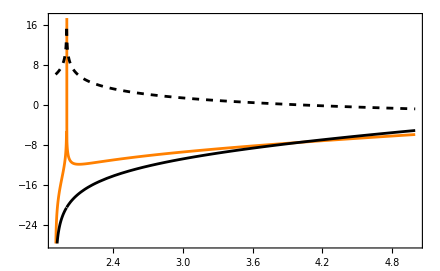

```mathematica
Plot[{hpcomp[rphys]+12,fks[rphys],dhpcomp[rphys]+12},{rphys,rphystrum,5},Frame->True,FrameLabel->{MaTeX["\\tilde r",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440,PlotStyle->{Orange,{Black,Dashed},Black},PlotLegends->Placed[Map[MaTeX[#,Magnification->1.4]&,{"h(\\tilde r)","f(\\tilde r)","\\Delta h(\\tilde r)"}],{Scaled[{0.2,0}],{0,-0.5}}]]//Quiet
```

#### Equations

```mathematica
us=(Exp[(tphysKS+rphys)/(4mass)]+(rphys/2/mass-1)Exp[-(tphysKS-rphys)/(4mass)])/2;
vs=(Exp[(tphysKS+rphys)/(4mass)]-(rphys/2/mass-1)Exp[-(tphysKS-rphys)/(4mass)])/2;
```

```mathematica
Us = ArcTan[us+vs]; Vs = ArcTan[us-vs];
```

```mathematica
Ts = (Us - Vs)/2; Rs = (Us+Vs)/2;
```

```mathematica
listtts[tval_]:= {Rs, Ts} /. {tphysKS -> tval+dhpcomp[rphys]}/.mass->massset;
```

#### Graphs

```mathematica
colourph=Black;
```

```mathematica
listttt={-15,-24,-27.75(*,-30.25*),-32.5(*,-36*)}+54(*taking awa some slices to better show comparison with previous method*)
hlist=Map[listtts[#]&,listttt];
```

{39,30,26.25,21.5}

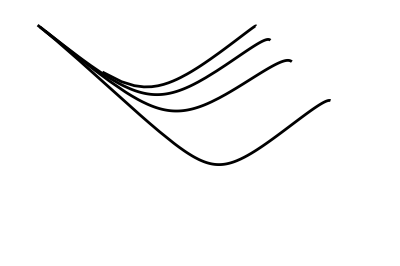

```mathematica
getclose=0.001;
hypfolpdh=ParametricPlot[hlist,{rphys,rphystrum+getclose,10},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourph,Axes->None,PlotPoints->200](*Show[{ParametricPlot[hlisto,{rphys,rphyshornum,20},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourph,Axes->None],ParametricPlot[hlisti,{rphys,rphystrum+getclose,rphyshornum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourph,Axes->None]}]*)
```

```mathematica
Show[{lettersschw,spacebh,hypfolpdh,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourph,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

```mathematica
Show[{lettersschw,spacebh,hypfolp,hypfolpdh,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const} \\textrm{ for } \\Delta h",Magnification->1.8],MaTeX["t=\\textrm{const} \\textrm{ for } h",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourph,colourp,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.12,0.24},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

```mathematica
(*Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/penrphysboth.pdf",%,"PDF"]*)
```

### Construction using the physical tortoise radial coordinate (only for closed-form expressions) -- in paper’s appendix

#### Height function

```mathematica
exprtag="closedform";
```

```mathematica
rphystrum=inmstR;
```

```mathematica
(*location of rphystrum on the tortoise radial coordinate*)
inmstrtort=rp+2massset Log[rp/(-2massset)+1]/.rp->rphystrum
```

-4.19050904376013200513988334012141507306

```mathematica
rp+2massset Log[-rp/(-2massset)-1]/.rp->4 massset
```

4

```mathematica
DSolve[rtort'[r]==1/(1-2mass/r),rtort,r]
```

{{rtort→Function[{r},r+C[1]+2 mass Log[-2 mass+r]]}}

{{rphys→InterpolatingFunction[…]}}

{{rphys→InterpolatingFunction[…]}}

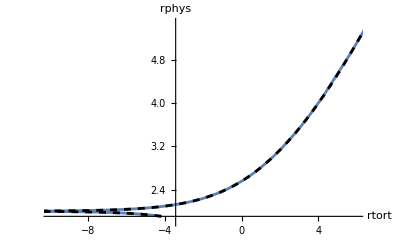

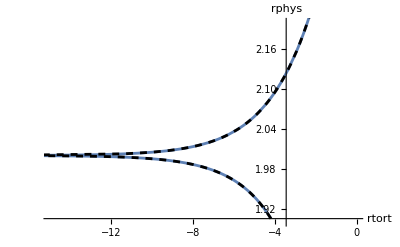

```mathematica
extrinin=-40;extrinout=inmstrtort;
extroutin=-40;extroutout=100;
NDSolve[{rphys'[rtort]==(1-2mass/rphys[rtort]),rphys[inmstrtort]==rphystrum}/.mass->massset,{rphys},{rtort,extrinin,extrinout}]
rphysin=%[[1,1,2]];
NDSolve[{rphys'[rtort]==(1-2mass/rphys[rtort]),rphys[4massset]==4massset(*r[extroutin]==rphysin[extrinin]*)}/.mass->massset,{rphys},{rtort,extroutin,extroutout}]
rphysout=%[[1,1,2]];
Show[{Plot[rphysin[rtort],{rtort,extrinin,extrinout},PlotRange->All],Plot[rphysout[rtort],{rtort,extroutin,extroutout},PlotRange->All],ParametricPlot[{rphys+2massset Log[1-rphys/(2massset)],rphys},{rphys,inmstR,2massset},PlotStyle->{Black,Dashed}],ParametricPlot[{rphys+2massset Log[rphys/(2massset)-1],rphys},{rphys,2massset,10},PlotStyle->{Black,Dashed}]},PlotRange->{{-10,6},{1.8,5.5}},AxesLabel->{rtort,rphys}]
Show[%,PlotRange->{{-15,0},{1.9,2.2}},AxesLabel->{rtort,rphys}]
```

```mathematica
grphysrphysc[rphys_]=χc[r]/αc[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2/.aconf->Function[{r},1]/.Q->0/.r->rphys
```

(9 rphys^4)/(9 Ccmc^2+6 (Ccmc Kcmc-3 mass) rphys^3+9 rphys^4+Kcmc^2 rphys^6)

```mathematica
βrphysc[rphys_]=Simplify[Simplify[-Sqrt[(αc[r]^2-Ω[r]^2(1-2mass aconf[r]/r+Q^2 aconf[r]^2/r^2))χc[r]/grr[r]]/.grr[r]->χc[r]/αc[r]^2(Ω[r]^2/aconf[r]^2(aconf[r]-r aconf'[r]))^2,Assumptions->{(aconf[r]-r aconf'[r])∈Reals,(aconf[r]-r aconf'[r])>0,Ω[r]∈Reals,Ω[r]>0,aconf[r]∈Reals,aconf[r]>0,αb[r]∈Reals,αb[r]>0,Kcmc r^3+3 Ccmc aconf[r]^3∈Reals,Kcmc r^3+3 Ccmc aconf[r]^3<0}]/.aconf->Function[{r},1]/.Q->0/.r->rphys,Assumptions->{(3 Ccmc+Kcmc rphys^3)∈Reals,(3 Ccmc+Kcmc rphys^3)<0}]
```

((3 Ccmc+Kcmc rphys^3) √(9 Ccmc^2+6 Ccmc Kcmc rphys^3+rphys^3 (-18 mass+9 rphys+Kcmc^2 rphys^3)))/(9 rphys^4)

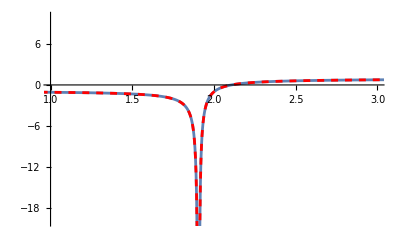

```mathematica
(1-(2 mass aconf[r])/r)Last@hfuncdcomp/.Ccmc->Ccmcset/.mass->massset/.Kcmc->Kcmcset/.allvalg[{aconf[r]->1}]//Evaluate;
Plot[%,{r,0,10},PlotRange->All]//Quiet;
hpptcomp[r_]=((-βrphysc[r]grphysrphysc[r]/χc[r])//Simplify)/.allvalg[{aconf[r]->1}]/.allvalg[{Ω[r]->1}]//.subvals//Evaluate;
Plot[%,{r,0,10},PlotStyle->{Red,Dashed},PlotRange->All]//Quiet;
Show[%%%,%,PlotRange->{{1,3},{-20,10}},AxesOrigin->{1,0}]//Quiet
```

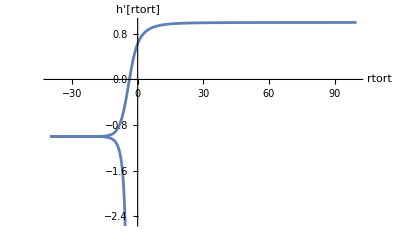

```mathematica
hpptout=Compile[{rt},Evaluate[hpptcomp[rphys]/.rphys->rphysout[rt]]];
Plot[hpptout[rt],{rt,extroutin,extroutout}]//Quiet;
hpptin=Compile[{rt},Evaluate[hpptcomp[rphys]/.rphys->rphysin[rt]]];
Plot[hpptin[rt],{rt,extrinin,extrinout},PlotRange->{-10,Automatic}]//Quiet;
Show[{%%%,%},PlotRange->{-2.5,1},AxesLabel->{"rtort","h'[rtort]"}]
```

```mathematica
NDSolve[{hout'[rout]==hpptout[rout],hout[-20]==0},hout,{rout,extroutin,extroutout}]
hptout=%[[1,1,2]];
NDSolve[{hin'[rin]==hpptin[rin],hin[-20]==0},hin,{rin,extrinin,extrinout}]
hptin=%[[1,1,2]];
```

CompiledFunction::cfsa: Argument rout at position 1 should be a machine-size real number.

{{hout→InterpolatingFunction[…]}}

CompiledFunction::cfsa: Argument rin at position 1 should be a machine-size real number.

NDSolve::ndsz: At rin == -4.19051, step size is effectively zero; singularity or stiff system suspected.

{{hin→InterpolatingFunction[{{-40., -4.19051}}, <>]}}

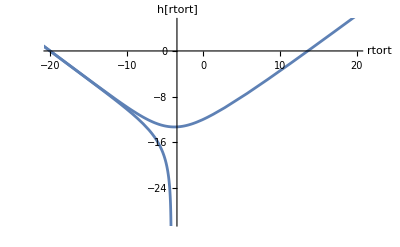

```mathematica
Show[{Plot[hptin[rtort],{rtort,extrinin,extrinout}],Plot[hptout[rtort],{rtort,extroutin,extroutout}]},PlotRange->{{-20,20},{-30,5}},AxesLabel->{"rtort","h[rtort]"}]
```

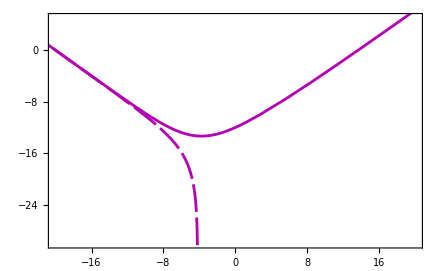

```mathematica
hptcolour=RGBColor[0.7,0,0.7];
Show[{Plot[hptin[rtort],{rtort,extrinin,extrinout},PlotStyle->{hptcolour,AbsoluteDashing[{20,4}]}],Plot[hptout[rtort],{rtort,extroutin,extroutout},PlotStyle->hptcolour]},PlotRange->{{-20,20},{-30,5}},Frame->True,FrameLabel->{MaTeX["\\tilde r_*",Magnification->1.4],MaTeX["h(\\tilde r_*)",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440]//Quiet
```

#### Equations

```mathematica
usot = Exp[rphyst/(4mass)]Cosh[tphys/(4mass)];vsot = Exp[rphyst/(4mass)]Sinh[tphys/(4mass)]; 
usit = Exp[rphyst/(4mass)]Sinh[tphys/(4mass)];vsit = Exp[rphyst/(4mass)]Cosh[tphys/(4mass)];
```

```mathematica
Usot = ArcTan[usot+vsot]; Vsot = ArcTan[usot-vsot];
Usit = ArcTan[usit+vsit]; Vsit = ArcTan[usit-vsit];
```

```mathematica
Tsot= (Usot - Vsot)/2; Rsot = (Usot+Vsot)/2;
Tsit= (Usit - Vsit)/2; Rsit = (Usit+Vsit)/2;
```

```mathematica
thsnumin= {tphys -> tphys + hptin[rphyst]};
thsnumout= {tphys -> tphys + hptout[rphyst]};
```

```mathematica
listttso[tval_]:= {Rsot, Tsot} /. thsnumout/. {tphys -> tval}/.mass->massset;
listttsi[tval_] := {Rsit, Tsit} /. thsnumin/. {tphys -> tval}/.mass->massset;
```

#### Graphs

```mathematica
colourpt=Directive[Black,DotDashed];
```

```mathematica
listttt={-15,-24,-27.75,-30.25,-32.5,-36}+43.4;(*chosen to coincide with hypfolp's*)
listttt={-15,-24,-27.75(*,-30.25*),-32.5(*,-36*)}+43.4;(*for better clarity in comparison diagram*)
hlisto=Map[listttso[#]&,listttt];
hlisti=Map[listttsi[#]&,listttt];
```

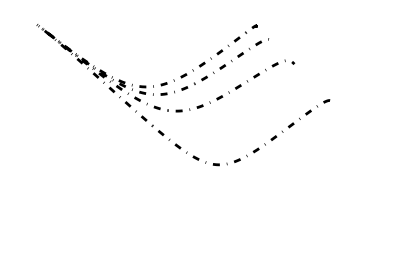

```mathematica
getclose=0.001;
rphystvalhor=-20;
hypfolpt=Show[{ParametricPlot[hlisto,{rphyst,rphystvalhor,40},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourpt,Axes->None],ParametricPlot[hlisti,{rphyst,rphystvalhor,extrinout-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourpt,Axes->None]}]
```

```mathematica
Show[{lettersschw,spacebh,hypfolp,hypfolpt,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}  \\textrm{ for } \\tilde r_*",Magnification->1.8],MaTeX["t=\\textrm{const} \\textrm{ for }\\tilde r",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourpt,colourp,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.12,0.24},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

### Construction using the compactified radial coordinate ---- generalise for any c?

#### Height function

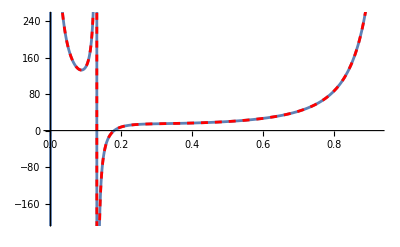

```mathematica
(*h'(r)*)
Last@hfuncdcomp/.Ccmc->Ccmcset/.mass->massset/.Kcmc->Kcmcset/.allvalg[{aconf[r]->lilu[r]}]//Evaluate;
Plot[%,{r,0,1}(*,PlotRange->{-20,5}*)]//Quiet;
hpccomp[r_]=((-βrc[r]grrc[r]/χc[r]/A)/.A->αc[r]^2-βrc[r]^2 grrc[r]/χc[r]//Simplify)//.subvals//Evaluate;
Plot[%,{r,0,1},PlotStyle->{Red,Dashed}]//Quiet;
Show[%%%,%,PlotRange->{-200,250}]//Quiet
```

```mathematica
FindRoot[(r/aconfc[r]//.subvals)==2massset,{r,0.1}]
rhornum=%[[1,2]](*location of the horizon in the compactified coordinates*)
```

{r→0.130552}

0.130552

NDSolve::ndsz: At r == 0.130552, step size is effectively zero; singularity or stiff system suspected.

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {2.667×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 0.130552, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1., step size is effectively zero; singularity or stiff system suspected.

{{hfu→InterpolatingFunction[…]}}

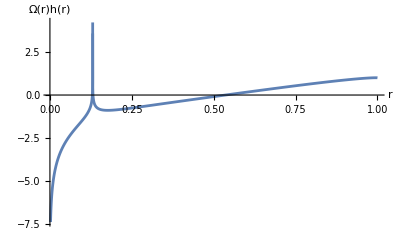

Piecewise[{{InterpolatingFunction[…][r], r<0.130552}, {InterpolatingFunction[…][r], r>0.130552}, {0, True}}]

```mathematica
closehor=0.001;
hpccomp[r];
NDSolve[{%==hfu'[r],hfu[rhornum-closehor]==0},hfu,{r,0.00003,(*0.99997*)1}]
Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)%[[1,1,2]][r],{r,0,rhornum}];
NDSolve[{%%%==hfu'[r],hfu[rhornum+closehor]==0},hfu,{r,0.00003,(*0.99997*)1}]
Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)%[[1,1,2]][r],{r,rhornum,1}];
Show[{%%%,%},PlotRange->All(*{-10,60}*),AxesLabel->{"r","Ω(r)h(r)"}]
hcnumcomp[r_]=Piecewise[{{%%%%%[[1,1,2]][r],r<rhornum},{%%%[[1,1,2]][r],r>rhornum}}]
```

```mathematica
(*setting the integration constant for the height function so that they conincide with the Minkowski one asymptotically -- using same condition as when integrating with the physical radial coordinate above*)
FindRoot[rphysmax==r/aconfc[r]//.subvals,{r,0.99999999}]
(hcnumcomp[r]+hc)==(minkheight/.rphys->r/Ω[r]/.omega/.rscri->1/.Kcmc->Kcmcset)/.%[[1]](* Mink and Schw h are expected to be the same asymptotically, comparing this -- however, cannot get too close to r=1, as the integrated Schwarzschild height function is not completely reliable there*)
Solve[%,hc]
hconstval=%[[1,1,2]];
```

{r→0.99997}

100015.+hc==99997.

{{hc→-18.4203}}

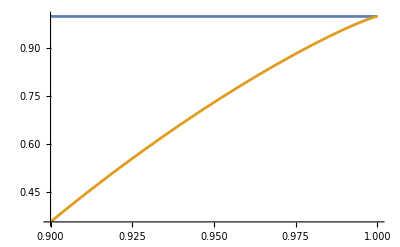

```mathematica
Clear@hccomp
hconst=hconstval;
Plot[{1,(hcnumcomp[r]+hconst)/(minkheight/.rphys->r/Ω[r]/.omega/.rscri->1/.Kcmc->Kcmcset)}//Evaluate,{r,0.9,1}(*,PlotRange->{0.99,1.01}*)]
hccomp[r_]=hcnumcomp[r]+hconst;(*adding an integration constant to the numerical h so that it coincides (as much as possible) with the Minkowski case at infinity (where the height function diverges)*)
```

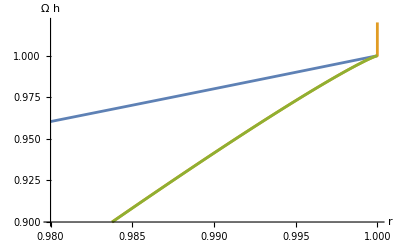
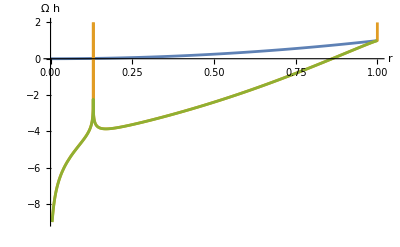

```mathematica
(*comparison between Ω rescaled Minkowski (blue) and Schwarzschild (green) height functions (optionally also with the height function calculated using the physical radius (yellow))*)
{Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys]/.rphys->r/lilu[r],hccomp[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0.98,1},PlotRange->{0.9,1.02},AxesLabel->{"r", "Ω h"},ImageSize->400],Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys]/.rphys->r/lilu[r],hccomp[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-9,2},AxesLabel->{"r", "Ω h"},ImageSize->400]}//Quiet
```

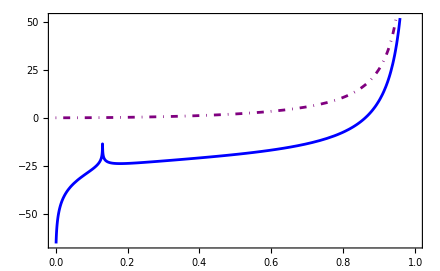
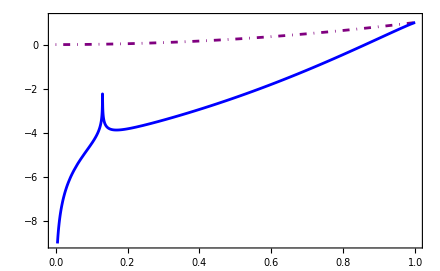

```mathematica
{Plot[{minkheight/.rphys->r/Ω[r],hccomp[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},Frame->True,FrameLabel->{MaTeX["
r",Magnification->1.4],MaTeX["h(r)",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440,PlotStyle->{{Purple, DotDashed},Blue}],Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hccomp[r]}/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-9,1.2},Frame->True,FrameLabel->{MaTeX["
r",Magnification->1.4],MaTeX["\\Omega(r)\,h(r)",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440,PlotStyle->{{Purple, DotDashed},Blue},PlotLegends->Placed[Map[MaTeX[#,Magnification->1.4]&,{"\\textrm{Minkowski}","\\textrm{Schwarzschild}"}],{Scaled[{0.5,0.1}],{0,0}}]]//Quiet}//Quiet
```

#### Equations

```mathematica
listttso[tval_]:= {Rso, Tso} /. {tphys -> tval+hccomp[r]}/.mass->massset/.rphys->r/aconf[r]/.subaconf;
listttsi[tval_] := {Rsi, Tsi} /. {tphys -> tval+ hccomp[r]}/.mass->massset/.rphys->r/aconf[r]/.subaconf;
```

#### Graphs

```mathematica
colourc=Red;
```

```mathematica
listttt=(*{-15,-20,-27,-30,-32,-35,-40}+40*){-15,-24,-27.75,-30.25,-32.5,-36}+54
hlisto=Map[Compile[{r},listttso[#]][r]&,listttt]//Quiet;
hlisti=Map[Compile[{r},listttsi[#]][r]&,listttt]//Quiet;
```

{39,30,26.25,23.75,21.5,18}

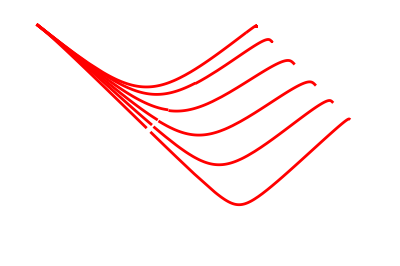

```mathematica
getclose=0.0005;hypfolc=Show[{ParametricPlot[hlisto,{r,rhornum+getclose,0.94},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourc,Axes->None(*,PlotPoints->20*)],ParametricPlot[hlisti,{r,0+getclose,rhornum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourc,Axes->None(*,PlotPoints->20*)]}]
```

```mathematica
Show[{lettersschw,spacebh,hypfolc,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourc,colourspatial},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

### Construction integrating for Δh = h - f in compactified Kerr-Schild coordinates ---- fix hconst for c different from 1?

#### Height function

```mathematica
1/(1-r/2/mass/aconf[r])((aconf[r]-r aconf'[r])/aconf[r]^2)(*Schwarzschild closed-form expression*)
dfkscomp=-((aconf[r]-r aconf'[r])/aconf[r]^2)(Ω[r]^2-A)/A/.A->αb[r]^2-βrb[r]^2 grrb[r]/χb[r]/.trumpetsubsb/.Q->0//Simplify(*expression from metric components*)
dfkscomp-%%//Simplify(*safety check*)
dfkscompc=-((aconfc[r]-r aconfc'[r])/aconfc[r]^2)(Ω[r]^2-A)/A/.omega/.rscri->1/.Kcmc->Kcmcset//Simplify(*expression from metric components*);
```

(aconf[r]-r aconf'[r])/((1-r/(2 mass aconf[r])) aconf[r]^2)

(2 mass (aconf[r]-r aconf'[r]))/(aconf[r] (-r+2 mass aconf[r]))

0

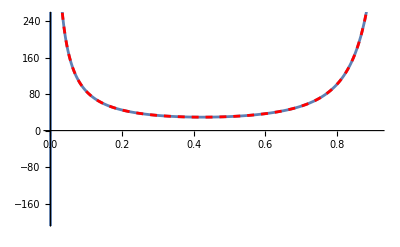

```mathematica
(*Δh'(r)*)
Last@hfuncdcomp-dfkscomp/.Ccmc->Ccmcset/.mass->massset/.Kcmc->Kcmcset/.allvalg[{aconf[r]->lilu[r]}]//Evaluate;
Plot[%,{r,0,1}]//Quiet;
dhpccomp[r_]=((-βrc[r]grrc[r]/χc[r]/c/A-dfkscompc)/.A->(αc[r]^2-βrc[r]^2 grrc[r]/χc[r])/c^2//Simplify)//.subvals//Evaluate;(*generalise!!*)
Plot[%,{r,0,1},PlotStyle->{Red,Dashed}]//Quiet;
Show[%%%,%,PlotRange->{-200,250}]//Quiet
```

```mathematica
FindRoot[(r/aconfc[r]//.subvals)==2massset,{r,0.1}]
rhornum=%[[1,2]](*location of the horizon in the compactified coordinates*)
```

{r→0.130552}

0.130552

NDSolve::ndsz: At r == 0.130552, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1., step size is effectively zero; singularity or stiff system suspected.

{{hfu→InterpolatingFunction[…]}}

NDSolve::ndsz: At r == 1.32929×10^-15, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 0.130552, step size is effectively zero; singularity or stiff system suspected.

{{hfu→InterpolatingFunction[…]}}

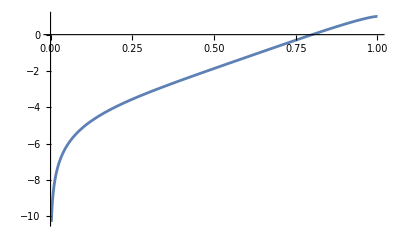

```mathematica
(*even if Δh' is continuous, it is 0/0 at the horizon and NDSolve cannot easily deal with it, so integrating separately and then joining*)
NDSolve[{dhpccomp[r]==hfu'[r],hfu[0.8]==0},hfu,{r,0,1}]
dhcnumout=%[[1,1,2]];
NDSolve[{dhpccomp[r]==hfu'[r],hfu[0.05]==0},hfu,{r,0,1}]
dhcnumpin=%[[1,1,2]];
dhcnumin[r_]=dhcnumpin[r]-dhcnumpin[rhornum-If[tvalindex>1,10^-8,0]]+dhcnumout[rhornum];(*setting the same integration constant for both parts*)
dhcnumcomp[r_]=Piecewise[{{dhcnumin[r],r<rhornum},{dhcnumout[r],r>rhornum}}];
Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)dhcnumcomp[r],{r,0,1}]
```

```mathematica
(*setting the integration constant for the height function so that they conincide with the Minkowski one asymptotically -- using same condition as when integrating with the physical radial coordinate above*)
FindRoot[rphysmax==r/aconfc[r]//.subvals,{r,0.99999999}]
(dhcnumcomp[r]+(fks[r/aconfc[r]]/.subaconf//.subvals)+hc)==(minkheight/.rphys->r/Ω[r]/.omega/.rscri->1/.Kcmc->Kcmcset)(*/.r->0.99*)(*/.r->0.992*)/.%[[1]](* Mink and Schw h are expected to be the same asymptotically, comparing this -- however, cannot get too close to r=1, as the integrated Schwarzschild height function is not completely reliable there*)
Solve[%,hc]
hconstval=%[[1,1,2]];
```

{r→0.99997}

100001.+hc==99997.

{{hc→-4.01909}}

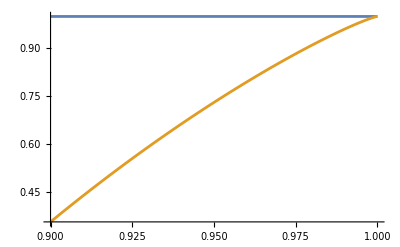

```mathematica
Clear@dhccomp
hconst=hconstval;
Plot[{1,(dhcnumcomp[r]+(fks[r/aconfc[r]]/.subaconf//.subvals)+hconst)/(minkheight/.rphys->r/Ω[r]/.omega/.rscri->1/.Kcmc->Kcmcset)}//Evaluate,{r,0.9,1}(*,PlotRange->{0.99,1.01}*)]
dhccomp[r_]=dhcnumcomp[r]+hconst(*-13.033930531918884*);(*adding an integration constant to the numerical h so that it coincides (as much as possible) with the Minkowski case at infinity (where the height function diverges)*)
```

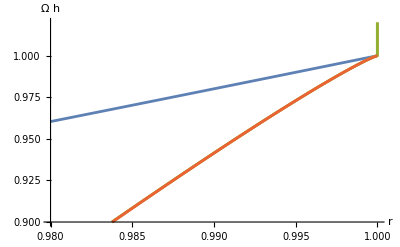
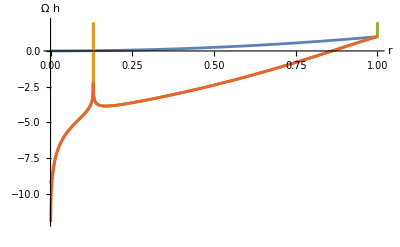
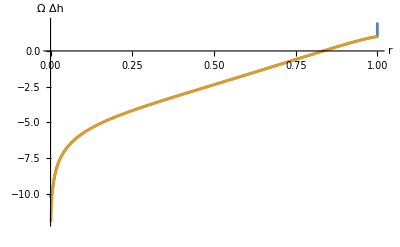

Schwarzschild lines may not coincide if data other than CMC Schwarzschild used.

```mathematica
(*left and middle: comparison between Ω rescaled height functions for Minkowski (blue) and Schwarzschild: integrating h with physical r(yellow), integrating Δh with physical r (green) and integrating Δh for compactified r (red)*)
(*right Ω Δh integrated with physical r (blue) and with compactified r (yellow)*)
{Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys],dhpcomp[rphys]+fks[rphys],dhccomp[r]+fks[rphys]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0.98,1},PlotRange->{0.9,1.02},AxesLabel->{"r", "Ω h"},ImageSize->400],Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hpcomp[rphys],dhpcomp[rphys]+fks[rphys],dhccomp[r]+fks[rphys]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-12,2},AxesLabel->{"r", "Ω h"},ImageSize->400],Plot[Ω[r]{(*minkheight/.rphys->r/Ω[r],*)dhpcomp[rphys],dhccomp[r]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-12,2},AxesLabel->{"r", "Ω Δh"},ImageSize->400]}//Quiet
Style["Schwarzschild lines may not coincide if data other than CMC Schwarzschild used.",Orange]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

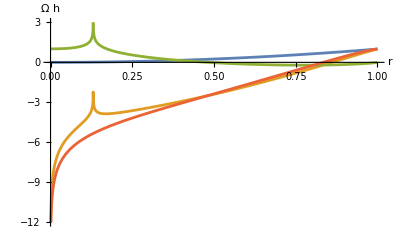

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

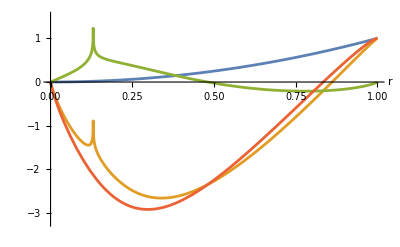

```mathematica
Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hccomp[r],fks[rphys],dhccomp[r]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-12,3},AxesLabel->{"r", "Ω h"},ImageSize->400]
Plot[{Ω[r]minkheight/.rphys->r/Ω[r],aconfc[r]hccomp[r],aconfc[r]fks[rphys],aconfc[r]dhccomp[r]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-3.2,1.5},AxesLabel->{"r"},ImageSize->400]
```

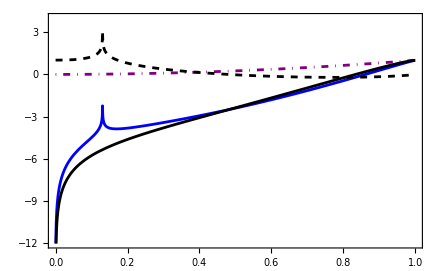
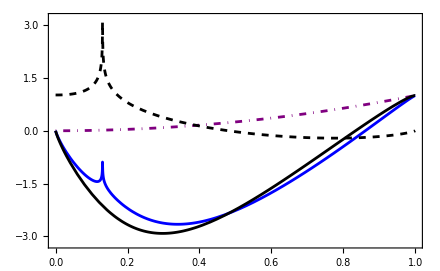

```mathematica
{Plot[Ω[r]{minkheight/.rphys->r/Ω[r],hccomp[r],fks[rphys],dhccomp[r]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-12,4},Frame->True,FrameLabel->{MaTeX["
r",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440,PlotStyle->{{Purple, DotDashed},Blue,{Black,Dashed},Black},PlotLegends->Placed[Map[MaTeX[#,Magnification->1.4]&,{"\\Omega\,h \\textrm{ (Mink)}","\\Omega\,h \\textrm{ (Schw)}","\\Omega\,f \\textrm{ (Schw)}","\\Omega\,\\Delta h \\textrm{ (Schw)}"}],{Scaled[{0.55,0.02}],{0,0}}]],Plot[{Ω[r]minkheight/.rphys->r/Ω[r],aconfc[r]hccomp[r],Ω[r]fks[rphys],aconfc[r]dhccomp[r]}/.rphys->r/aconfc[r]/.subaconf/.omega/.rscri->1/.Kcmc->Kcmcset//Evaluate,{r,0,1},PlotRange->{-3.2,3.2},Frame->True,FrameLabel->{MaTeX["r",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440,PlotStyle->{{Purple, DotDashed},Blue,{Black,Dashed},Black},PlotLegends->Placed[Map[MaTeX[#,Magnification->1.4]&,{"\\Omega\,h \\textrm{ (Mink)}","\\bar\\Omega\,h \\textrm{ (Schw)}","\\Omega\,f \\textrm{ (Schw)}","\\bar\\Omega\,\\Delta h \\textrm{ (Schw)}"}],{Scaled[{0.25,1}],{0,01}}]]//Quiet}//Quiet
```

#### Equations

```mathematica
us=(Exp[(tphysKS+rphys)/(4mass)]+(rphys/2/mass-1)Exp[-(tphysKS-rphys)/(4mass)])/2;
vs=(Exp[(tphysKS+rphys)/(4mass)]-(rphys/2/mass-1)Exp[-(tphysKS-rphys)/(4mass)])/2;
```

```mathematica
Us = ArcTan[us+vs]; Vs = ArcTan[us-vs];
```

```mathematica
Ts = (Us - Vs)/2; Rs = (Us+Vs)/2;
```

```mathematica
listtts[tval_]:= {Rs, Ts} /. {tphysKS -> tval+dhccomp[r]}/.mass->massset/.rphys->r/aconf[r]/.subaconf;
```

#### Graphs

```mathematica
colourch=Brown;
```

```mathematica
listttt=(*{(*-15,*)-20,-27,-30,-32,-35,-40}+25*){-15,-24,-27.75,-30.25,-32.5,-36}+54(*+22*)
hlist=Map[listtts[#]&,listttt];
```

{39,30,26.25,23.75,21.5,18}

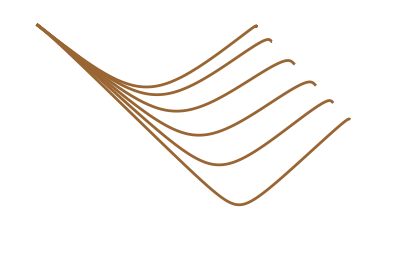

```mathematica
getclose=0.001;
hypfolcdh=ParametricPlot[hlist,{r,0+getclose,1-0.06},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourch,Axes->None,PlotPoints->200]
```

```mathematica
Show[{lettersschw,spacebh,hypfolcdh,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourch,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

#### Graphs (non CMC slices) for “imitateoldoslong” output data

```mathematica
colourchnoncmc=Directive[Black];
```

```mathematica
listttt=(*{(*-15,*)-20,-27,-30,-32,-35,-40}+25*){-15,-24,-27.75,-30.25,-32.5,-36}+54(*+22*)
hlist=Map[listtts[#]&,listttt];
```

{39,30,26.25,23.75,21.5,18}

```mathematica
listttt={(*-15,*)-20,-27,-30,-32,-35,-40}+40
hlisto=Map[Compile[{r},listttso[#]][r]&,listttt]//Quiet;
hlisti=Map[Compile[{r},listttsi[#]][r]&,listttt]//Quiet;
```

{20,13,10,8,5,0}

InterpolatingFunction::dmval: Input value {-3.69993} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

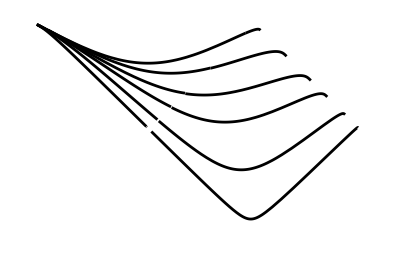
{53.2135,-Graphics-}

```mathematica
(*takes a long time to evaluate -- see below for a much faster option*)
Timing[getclose=0.0005;
rctvalhor=plotfrom(*+0.2*)+0.5;
hypfolctnoncmc=Show[{ParametricPlot[hlisto,{rout,rctvalhor,1(*/c*)-200getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None],ParametricPlot[hlisti,{rin,rctvalhor,rcttrum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None]}]]
```

```mathematica
Show[{lettersschw,spacebh,hypfolctnoncmc,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourctnoncmc,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

Optionally, can also use the following to plot, where the final quantities are expressed in terms of the compactified radial coordinate instead of the conformal tortoise one -- making the plot is much faster and the region around the horizon looks better.

```mathematica
thsnumin= {tphys ->tphys + hctin[rin]/.rin->rtcnumin[r]};
thsnumout= {tphys ->tphys+ hctout[rout]/.rout->rtcnumout[r]};
listttso[tval_] := {Rso, Tso} /. thsnumout/. {tphys-> tval}/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc
listttsi[tval_] := {Rsi, Tsi} /. thsnumin/. {tphys-> tval}/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc
```

```mathematica
listttt={(*-15,*)-20,-27,-30,-32,-35,-40}+40
hlisto=Map[Compile[{r},listttso[#]][r]&,listttt]//Quiet;
hlisti=Map[Compile[{r},listttsi[#]][r]&,listttt]//Quiet;
```

{20,13,10,8,5,0}

InterpolatingFunction::dmval: Input value {-4.32306} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

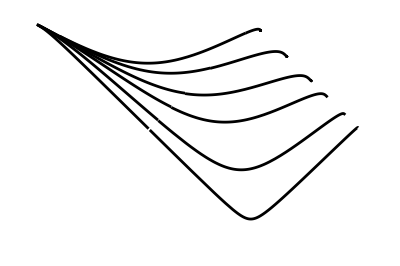
{0.336774,-Graphics-}

```mathematica
Timing[getclose=0.0001;(*imitateoldoslong_*)hypfolctnoncmc=Show[{ParametricPlot[hlisto,{r,rhornum+getclose,0.94},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None(*,PlotPoints->20*)],ParametricPlot[hlisti,{r,0+0.002,rhornum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None(*,PlotPoints->20*)]}]]
```

```mathematica
Show[{lettersschw,spacebh,hypfolctnoncmc,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourctnoncmc,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

### Construction using the compactified tortoise radial coordinate -- in paper’s appendix

#### Height function

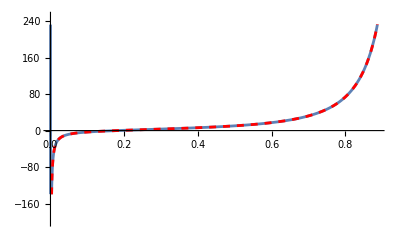

```mathematica
(*dr/drtort h'(r)*)
(1-2mass aconf[r]/r)Last@hfuncdcomp/.omega/.rscri->1/.Ccmc->Ccmcset/.mass->massset/.Kcmc->Kcmcset/.allvalg[{aconf[r]->lilu[r]}]//Evaluate;
Plot[%,{r,0,1}(*,PlotRange->{-20,5}*)]//Quiet;
hpctcomp[r_]=((-βrc[r]grrc[r]/χc[r]/Ω[r]^2/.omega/.Kcmc->Kcmcset/.rscri->1)//Simplify)//.subvals//Evaluate;
Plot[%,{r,0,1},PlotStyle->{Red,Dashed}]//Quiet;
Show[%%%,%,PlotRange->{-200,250}]//Quiet
```

```mathematica
FindRoot[(r/aconfc[r]//.subvals)==2massset,{r,0.1}]
rhornum=%[[1,2]]
```

{r→0.130552}

0.130552

NDSolve::ndsz: At r == 0.130552, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {r,rtc[r]} = {1.,1.}.

{{rtc→InterpolatingFunction[…]}}

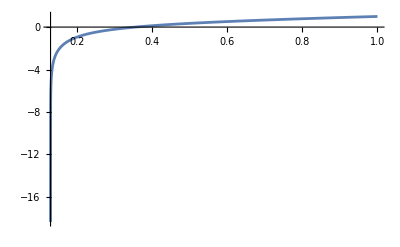

-10.9672

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {r,rtc[r]} = {0.,1.06239}.

NDSolve::ndsz: At r == 0.130552, step size is effectively zero; singularity or stiff system suspected.

{{rtc→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {2.667×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

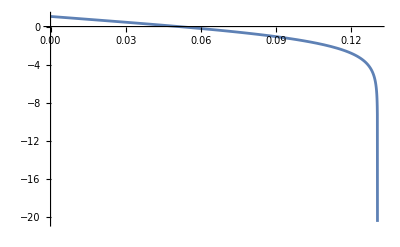

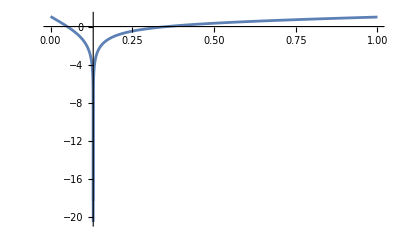

```mathematica
(*matching at the horizon*)
Which[exprtag=="closedform",closehor=0.00001;,exprtag=="numerical",closehor=0.0001;]
Which[exprtag=="closedform",close2scri=10^-8;,exprtag=="numerical",close2scri=10^-6;]
NDSolve[{(1/(A/Ω[r]^2/.omega/.Kcmc->Kcmcset/.rscri->1)/.A->(αc[r]^2-βrc[r]^2 grrc[r]/χc[r])/c^2//.subvals)==rtc'[r],rtc[1-close2scri]==1(*/c*)(*is this the correct condition at infinity? use "c" here??*)},rtc,{r,0,1}]
rtcnumout=%[[1,1,2]];
Plot[rtcnumout[r],{r,rhornum,1},PlotRange->All(*{-6,Automatic}*)]
rtcnumout[rhornum+closehor]
NDSolve[{(1/(A/Ω[r]^2/.omega/.Kcmc->Kcmcset/.rscri->1)/.A->(αc[r]^2-βrc[r]^2 grrc[r]/χc[r])/c^2//.subvals)==rtc'[r],rtc[rhornum-closehor]==%},rtc,{r,0,1}]
rtcnumin=%[[1,1,2]];
Plot[rtcnumin[r],{r,0,rhornum},PlotRange->All]
Show[{%%%%%,%},PlotRange->{-6,Automatic}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{r→InverseFunction[InterpolatingFunction[…],1,1][rin]}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{r→InverseFunction[InterpolatingFunction[…],1,1][rout]}}

InterpolatingFunction::dmval: Input value {0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.04233

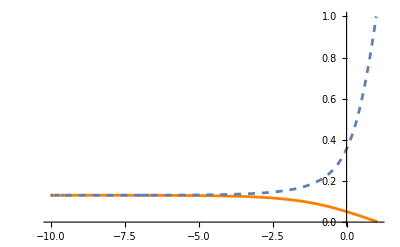

```mathematica
NSolve[rin==rtcnumin[r],r]
r2numrin=%[[1,1]];
NSolve[rout==rtcnumout[r],r]
r2numrout=%[[1,1]];
rcttrum=rtcnumin[0.001](*location of the trumpet in the compactified tortoise coordinate*)
Show[Plot[r/.r2numrin,{rin,-10,rcttrum},PlotStyle->Orange,PlotRange->All],Plot[r/.r2numrout,{rout,-10,1},PlotStyle->Dashed,PlotRange->All],PlotRange->All]
```

```mathematica
outexprnum=Compile[rout,(-βrc[r]grrc[r]/χc[r]/Ω[r]^2/.omega/.Kcmc->Kcmcset/.rscri->1)//.subvals/.r2numrout//Evaluate]
inexprnum=Compile[rin,(-βrc[r]grrc[r]/χc[r]/Ω[r]^2/.omega/.Kcmc->Kcmcset/.rscri->1)//.subvals/.r2numrin//Evaluate]
```

3
                         -3.114839973711186876968031808295289455628 InterpolatingFunction[{{0, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>][InverseFunction[InterpolatingFunction[{{0.130552, 1.}}, <>], 1, 1][rout]]    InverseFunction[InterpolatingFunction[{{0.130552, 1.}}, <>], 1, 1][rout]
                         -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------
                                                                                                                                                                                        2                                                                                                                              3
                                                                                                                InverseFunction[InterpolatingFunction[{{0.130552, 1.}}, <>], 1, 1][rout]
CompiledFunction[{rout}, -----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, -CompiledCode-]
                                                                                                                                                                                                                                                                                                2
                                                                                    InterpolatingFunction[{{0, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>][InverseFunction[InterpolatingFunction[{{0.130552, 1.}}, <>], 1, 1][rout]]

3
                        -3.114839973711186876968031808295289455628 InterpolatingFunction[{{0, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>][InverseFunction[InterpolatingFunction[{{0.0031443, 0.130552}}, <>], 1, 1][rin]]    InverseFunction[InterpolatingFunction[{{<<9>>, <<7>>2}}, <>], 1, 1][rin]
                        -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------
                                                                                                                                                                                             2                                                                                                                              3
                                                                                                               InverseFunction[InterpolatingFunction[{{0.0031443, 0.130552}}, <>], 1, 1][rin]
CompiledFunction[{rin}, -----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, -CompiledCode-]
                                                                                                                                                                                                                                                                                                     2
                                                                                   InterpolatingFunction[{{0, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>][InverseFunction[InterpolatingFunction[{{0.0031443, 0.130552}}, <>], 1, 1][rin]]

```mathematica
(*Which[exprtag=="closedform",interpfrom=-9;,exprtag=="numerical",interpfrom=-9(*7*);]*)
interpfrom=-9;
If[tvalindex>1,interpfrom=-4.5]
plotfrom=interpfrom+1;
setzero=plotfrom+2;
If[tvalindex>1,plotfrom=interpfrom+0.3;setzero=plotfrom+0.8]
```

```mathematica
exproutnum=Interpolation[Map[{#,outexprnum[#]/c}&,Range[interpfrom,1(*/c*),0.01]]]//Quiet
exprinnum=Interpolation[Map[{#,inexprnum[#]/c}&,Range[interpfrom,rcttrum,0.01]]]//Quiet
```

InterpolatingFunction[{{-9., 1.}}, <>]

InterpolatingFunction[…]

```mathematica
NDSolve[{hout'[rout]==exproutnum[rout],hout[setzero]==0},hout,{rout,plotfrom,1(*/c*)}]
hctout=%[[1,1,2]]
NDSolve[{hin'[rin]==exprinnum[rin],hin[setzero]==0},hin,{rin,plotfrom,rcttrum}]
hctin=%[[1,1,2]]
```

NDSolve::nlnum: The function value {-1.70092 - 0.00141259 (0.00858741 <<1>> - 100. (1.70092 + Divide[Divide[-3.11484 Power[InterpolatingFunction[{{0., 1.}}, <>][InverseFunction[InterpolatingFunction[{{0.130552, 1.}}, <>], 1, 1][-6.74]], 3], Power[InverseFunction[<<3>>][-6.74], 2]] + 0.333333 <<1>>, Power[<<2>>]]))} is not a list of numbers with dimensions {1} at {rout,hout[rout]} = {-6.73141,1.23965}.

NDSolve::nlnum: The function value {30200.4 - 0.00129452 (2.25999 Power[10, 6] + 0.00870548 <<1>>)} is not a list of numbers with dimensions {1} at {rout,hout[rout]} = {0.988705,277.115}.

{{hout→InterpolatingFunction[…]}}

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {1.04233} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{hin→InterpolatingFunction[…]}}

InterpolatingFunction[…]

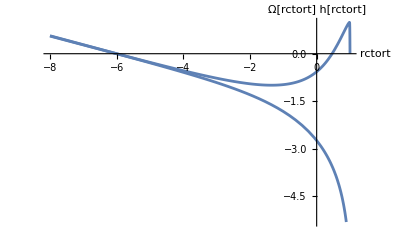

```mathematica
Show[{Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1) hctin[rin]/.r2numrin,{rin,plotfrom,rcttrum}],Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)hctout[rout]/.r2numrout,{rout,plotfrom,1(*/c*)}]},PlotRange->All,AxesLabel->{"rctort","Ω[rctort] h[rctort]"}]//Quiet
```

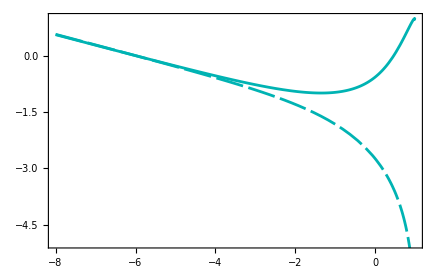

```mathematica
hctcolour=RGBColor[0,0.7,0.7];
Show[{Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)hctin[rin]/.r2numrin,{rin,plotfrom,rcttrum},PlotStyle->{hctcolour,AbsoluteDashing[{20,4}]}],Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)hctout[rout]/.r2numrout,{rout,plotfrom,0.99},PlotStyle->hctcolour]},PlotRange->{{-8,1},{-5,1}},Frame->True,FrameLabel->{MaTeX["r_*",Magnification->1.4],MaTeX["\\Omega(r_*)\,h(r_*)",Magnification->1.4]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameStyle->Black,BaseStyle->{FontSize->14},ImageSize->440]//Quiet
```

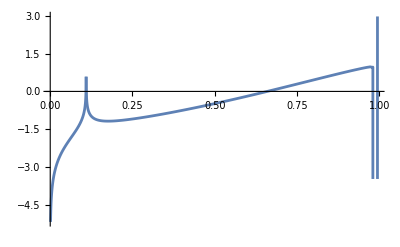

```mathematica
Show[{Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1) hctin[rin]/.rin->rtcnumin[r],{r,0,rhornum-closehor}],Plot[(Ω[r]/.omega/.Kcmc->Kcmcset/.rscri->1)hctout[rout]/.rout->rtcnumout[r],{r,rhornum+closehor,1(*/c*)}]},PlotRange->All]//Quiet
```

#### Equations

```mathematica
thsnumin= {tphys -> tphys + hctin[rin]};
thsnumout= {tphys -> tphys + hctout[rout]};
```

```mathematica
listttso[tval_]:= {Rso, Tso} /. thsnumout/. {tphys -> tval}/.mass->massset/.rphys->r/aconf[r]/.r2numrout/.subaconf;listttsi[tval_]:= {Rsi, Tsi} /. thsnumin/. {tphys -> tval}/.mass->massset/.rphys->r/aconf[r]/.r2numrin/.subaconf;
```

#### Graphs (CMC)

```mathematica
colourct=Directive[Blue];
```

```mathematica
listttt={(*-15,*)-20,-27,-30,-32,-35,-40}+40
hlisto=Map[Compile[{r},listttso[#]][r]&,listttt]//Quiet;
hlisti=Map[Compile[{r},listttsi[#]][r]&,listttt]//Quiet;
(*hlisto=Map[listttso[#]&,listttt];
hlisti=Map[listttsi[#]&,listttt];*)
```

{20,13,10,8,5,0}

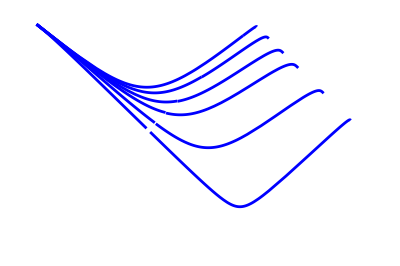

```mathematica
getclose=0.0005;
rctvalhor=plotfrom+1.5;
hypfolct=Show[{ParametricPlot[hlisto,{rout,rctvalhor,1(*/c*)-200getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourct,Axes->None],ParametricPlot[hlisti,{rin,rctvalhor,rcttrum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourct,Axes->None]}]
```

```mathematica
Show[{lettersschw,spacebh,hypfolct,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourct,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

#### Graphs (non CMC slices) for “imitateoldoslong” output data

```mathematica
colourctnoncmc=Directive[Black];
```

```mathematica
listttt={(*-15,*)-20,-27,-30,-32,-35,-40}+40
hlisto=Map[Compile[{r},listttso[#]][r]&,listttt]//Quiet;
hlisti=Map[Compile[{r},listttsi[#]][r]&,listttt]//Quiet;
```

{20,13,10,8,5,0}

```mathematica
(*takes a long time to evaluate -- see below for a much faster option*)
Timing[getclose=0.0005;
rctvalhor=plotfrom(*+0.2*)+0.5;
hypfolctnoncmc=Show[{ParametricPlot[hlisto,{rout,rctvalhor,1(*/c*)-200getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None],ParametricPlot[hlisti,{rin,rctvalhor,rcttrum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None]}]]
```

InterpolatingFunction::dmval: Input value {-3.69993} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{53.2135,-Graphics-}

```mathematica
Show[{lettersschw,spacebh,hypfolctnoncmc,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourctnoncmc,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

Optionally, can also use the following to plot, where the final quantities are expressed in terms of the compactified radial coordinate instead of the conformal tortoise one -- making the plot is much faster and the region around the horizon looks better.

```mathematica
thsnumin= {tphys ->tphys + hctin[rin]/.rin->rtcnumin[r]};
thsnumout= {tphys ->tphys+ hctout[rout]/.rout->rtcnumout[r]};
listttso[tval_] := {Rso, Tso} /. thsnumout/. {tphys-> tval}/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc
listttsi[tval_] := {Rsi, Tsi} /. thsnumin/. {tphys-> tval}/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc
```

```mathematica
listttt={(*-15,*)-20,-27,-30,-32,-35,-40}+40
hlisto=Map[Compile[{r},listttso[#]][r]&,listttt]//Quiet;
hlisti=Map[Compile[{r},listttsi[#]][r]&,listttt]//Quiet;
```

{20,13,10,8,5,0}

```mathematica
Timing[getclose=0.0001;(*imitateoldoslong_*)hypfolctnoncmc=Show[{ParametricPlot[hlisto,{r,rhornum+getclose,0.94},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None(*,PlotPoints->20*)],ParametricPlot[hlisti,{r,0+0.002,rhornum-getclose},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourctnoncmc,Axes->None(*,PlotPoints->20*)]}]]
```

InterpolatingFunction::dmval: Input value {-4.32306} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.336774,-Graphics-}

```mathematica
Show[{lettersschw,spacebh,hypfolctnoncmc,inrad,R0val,coverschw},Epilog->makePlotLegend[{MaTeX["t=\\textrm{const}",Magnification->1.8],MaTeX["\\tilde r=\\textrm{const}",Magnification->1.8]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourctnoncmc,Directive[colourspatial,Dashed,AbsoluteThickness[1]]},{0.22,0.22},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-

## Dynamical

## Trumpet relaxation

### Load data

```mathematica
tagdiag="imitateoldoslong";
diagdatam=Array[0,25-9];
Rm=Array[0,25-9];
Tm=Array[0,25-9];
Do[
filenamesdiag={repolocation<>"HypPenroseDiagrams/data/"<>tagdiag<>"m"<>ToString[num+9]<>"_diag_R_c4_single.yg",repolocation<>"HypPenroseDiagrams/data/"<>tagdiag<>"m"<>ToString[num+9]<>"_diag_T_c4_single.yg"};
Print[tagdiag<>"m"<>ToString[num+9]];
varddiag=Map[{ReadPygraph[#]}&,filenamesdiag];
diagdatam[[num]]=Table[{varddiag[[1,1,ct,1]],Table[{varddiag[[1,1,ct,2,st,2]],varddiag[[2,1,ct,2,st,2]]},{st,1,Length@varddiag[[1,1,ct,2]]}]},{ct,1,Length@varddiag[[1,1]]}];
Rm[[num]]=varddiag[[1,1]];
Tm[[num]]=varddiag[[2,1]];
,{num,1,25-9}]
```

imitateoldoslongm10

read 2690.71 KByte of data;

read 2693.52 KByte of data;

imitateoldoslongm11

read 2688.84 KByte of data;

read 2693.52 KByte of data;

imitateoldoslongm12

read 2686.75 KByte of data;

read 2693.38 KByte of data;

imitateoldoslongm13

read 2684.49 KByte of data;

read 2693.14 KByte of data;

imitateoldoslongm14

read 2682.06 KByte of data;

read 2692.91 KByte of data;

imitateoldoslongm15

read 2679.59 KByte of data;

read 2692.09 KByte of data;

imitateoldoslongm16

read 2677.05 KByte of data;

read 2691.46 KByte of data;

imitateoldoslongm17

read 2674.43 KByte of data;

read 2690.13 KByte of data;

imitateoldoslongm18

read 2671.84 KByte of data;

read 2688.68 KByte of data;

imitateoldoslongm19

read 2669.25 KByte of data;

read 2686.19 KByte of data;

imitateoldoslongm20

read 10060.5 KByte of data;

read 10076.8 KByte of data;

imitateoldoslongm21

read 2664.18 KByte of data;

read 2679.74 KByte of data;

imitateoldoslongm22

read 2661.82 KByte of data;

read 2676.29 KByte of data;

imitateoldoslongm23

read 2659.59 KByte of data;

read 2672.78 KByte of data;

imitateoldoslongm24

read 2657.75 KByte of data;

read 2669.2 KByte of data;

imitateoldoslongm25

read 2656.49 KByte of data;

read 2665.66 KByte of data;

### Evolution plots

```mathematica
relaxframes=Table[Show[lettersschw,ListLinePlot[Table[diagdatam[[num,ct,2]],{num,1,25-9}],PlotRange->{{-π/4,π/2},{-π/4,π/4}},AspectRatio->2/3],coverschw,ImageSize->{Automatic,400}],{ct,1,(*50*)Length@diagdatam[[1]]}];
```

```mathematica
ListAnimate[relaxframes,AnimationRunning->False]
```

```mathematica
Export[repolocation<>"HypPenroseDiagrams/gifs/trumrelax.gif",relaxframes,"DisplayDurations"->0.1]
```

~/other_repos/paper_repos/HypPenroseDiagrams/gifs/trumrelax.gif

```mathematica
(*to export each frame as png image -- suitable for use with LaTeX beamer's animate package*)
(*Export[repolocation<>"HypPenroseDiagrams/gifs/trumrelax_000.png",relaxframes,"VideoFrames"]*)
```

### Static plots

#### Comparison between initial CMC and final stationary slices

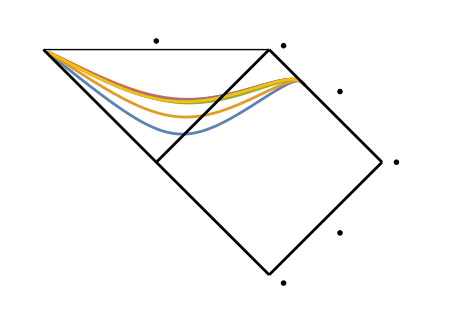
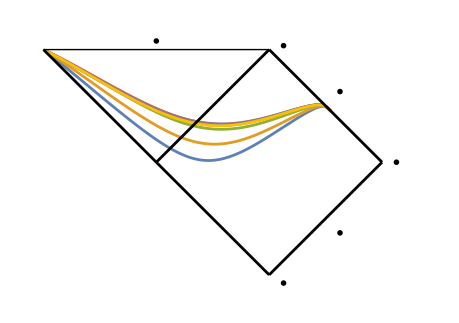
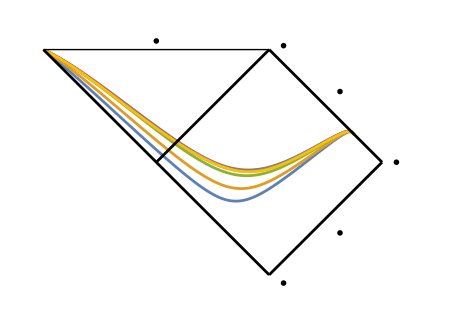
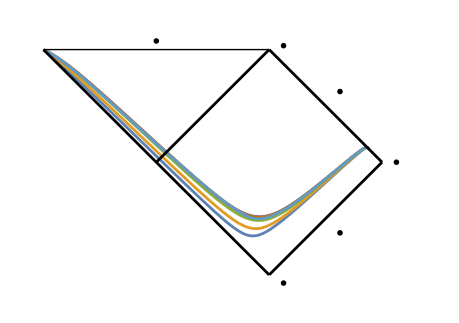

Superposition of (R,T) data corresponding to initial data for different initial t_0 at the times when they overlap at scri+, so showing the change in the trumpet slice as if time was not flowing.

```mathematica
{Show[lettersschw,ListLinePlot[Map[diagdatam[[#,#,2]]&,Range[1,8]],PlotRange->{{-π/4,π/2},{-π/4,π/4}},AspectRatio->2/3,Axes->None],coverschw,ImageSize->460],Show[lettersschw,ListLinePlot[Map[diagdatam[[#+3,#,2]]&,Range[1,8]],PlotRange->{{-π/4,π/2},{-π/4,π/4}},AspectRatio->2/3,Axes->None],coverschw,ImageSize->460],Show[lettersschw,ListLinePlot[Map[diagdatam[[#+6,#,2]]&,Range[1,8]],PlotRange->{{-π/4,π/2},{-π/4,π/4}},AspectRatio->2/3,Axes->None],coverschw,ImageSize->460],Show[lettersschw,ListLinePlot[Map[diagdatam[[#+9,#,2]]&,Range[1,7]],PlotRange->{{-π/4,π/2},{-π/4,π/4}},AspectRatio->2/3,Axes->None],coverschw,ImageSize->460]}
Style["Superposition of (R,T) data corresponding to initial data for different initial t_0 at the times when they overlap at scri+, so showing the change in the trumpet slice as if time was not flowing.",Blue]
```

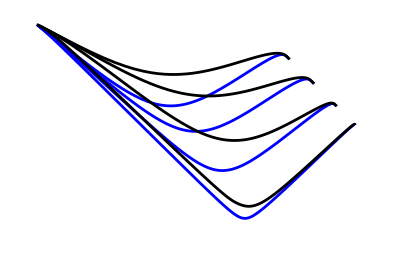

```mathematica
compar2cmc=ListLinePlot[{diagdatam[[1,1,2]],diagdatam[[10,10,2]],diagdatam[[4,1,2]],diagdatam[[8,5,2]],diagdatam[[7,1,2]],diagdatam[[11,5,2]],diagdatam[[12,1,2]],diagdatam[[16,5,2]]},PlotRange->{{-π/4,π/2},{-π/4,π/4}},AspectRatio->2/3,PlotStyle->{Blue,Black},Axes->None]
```

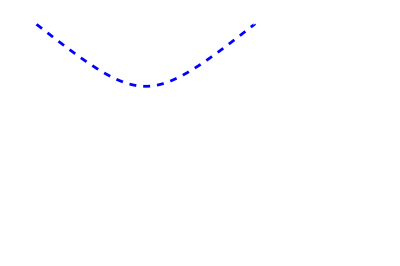

InterpolatingFunction::dmval: Input value {0.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

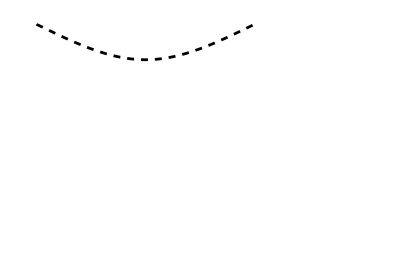

```mathematica
getclose=0.001;
listrsicmc[rval_] = {Rsi, Tsi} /.mass->massset/.rphys->r/lilu[r]/. {r -> rval};
inradcmc=Show[ParametricPlot[listrsicmc[0+getclose],{tphys,-100,80},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->{Blue,AbsoluteThickness[2],Dashed},Axes->None]]
(*the following assumes that aconfc corresponds to the non-CMC final stationary state*)
listrsinoncmc[rval_] = {Rsi, Tsi} /.mass->massset/.rphys->r/aconfc[r]/. {r -> rval};
inradstatio=Show[ParametricPlot[listrsinoncmc[0+getclose],{tphys,-100,80},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->{Black,AbsoluteThickness[2],Dashed},Axes->None]]
```

```mathematica
dyncompar2cmc=Show[lettersschw,inradcmc,inradstatio,compar2cmc,coverschw,Epilog->{makePlotLegend[{"CMC","stationary"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Blue,Black},{0.02,0.58},labe-2,labe-2,"Times"],makePlotLegend[{"CMC  trumpet","stationary  trumpet"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[Blue,Dashed],Directive[Black,Dashed]},{0.02,0.26},labe-2,labe-2,"Times"]},ImageSize->460]
```

-Graphics-

```mathematica
(*Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/dyn_compar2cmc.pdf",dyncompar2cmc,"PDF"]*)
```

#### Comparison between height-function calculated (using tortoise coordinate) and eikonal evolved non-CMC stationary data

```mathematica
(*construct R and T for the height function integrated in the compactified tortoise radial coordinate and express them in terms of the compactified radial coordinate for ease of comparison*)
thsnumin= {tphys -> t + hctin[rin]/.rin->rtcnumin[r]};
thsnumout= {tphys ->t+ hctout[rout]/.rout->rtcnumout[r]};
Rsall=Compile[{t,r},Piecewise[{{(Rso/. thsnumout/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc//Evaluate),r>rhornum},{(Rsi/. thsnumin/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc//Evaluate),r<rhornum}}]//Evaluate];
Tsall=Compile[{t,r},Piecewise[{{(Tso/. thsnumout/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc//Evaluate),r>rhornum},{(Tsi/. thsnumin/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc//Evaluate),r<rhornum}}]//Evaluate];
```

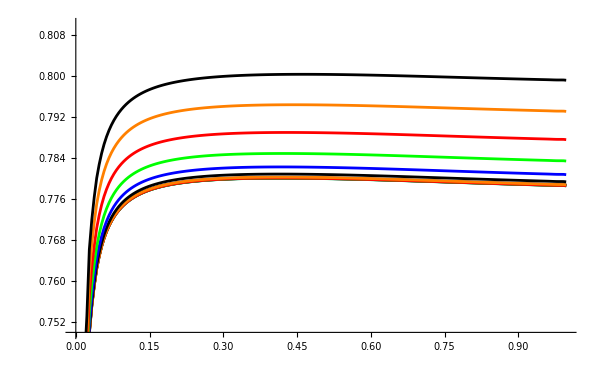

Beyond m20 (towards m25), data does not seem to be as reliable ... (All lines should lie on top of each other).

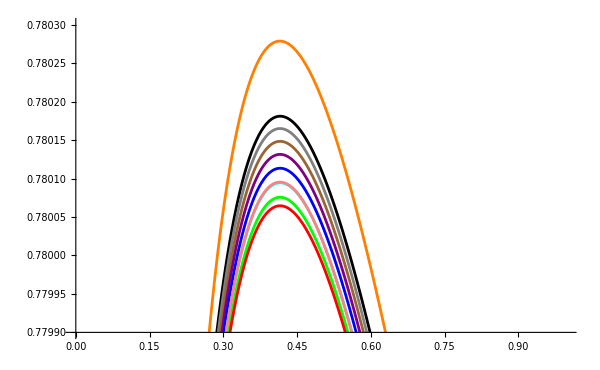

```mathematica
ListLinePlot[Map[Tm[[#,#+15,2]]&,Range[1,16]],PlotRange->{0.75,0.81},ImageSize->600,PlotStyle->{Black, Blue, Green, Red,Orange}]
Style["Beyond m20 (towards m25), data does not seem to be as reliable ... (All lines should lie on top of each other).",Red]
ListLinePlot[Map[Tm[[#,#+15,2]]&,Range[1,10]],PlotRange->{0.7799,0.7803},ImageSize->600,PlotStyle->{Black,Gray,Brown,Purple, Blue,Cyan, Green, Red,Pink,Orange}]
```

```mathematica
Rlegend=LineLegend[{Directive[Orange,AbsoluteThickness[1]],Directive[Orange,DotDashed,AbsoluteThickness[1]],Directive[Gray,Dashed,AbsoluteThickness[3]],Directive[Red,AbsoluteThickness[1]],Directive[Red,DotDashed,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[3]]},Map[Style[#,14,Black,FontFamily->"Times"]&,Flatten[{{"t_0 = -13 to t = 10","t_0 = -17 to t = 14", "Height for t = 19.6"},{"t_0 = -13 to t = 14","t_0 = -17 to t = 18", "Height for t = 23.6"}},1]],LegendLayout->{"Column",2},LegendMarkerSize->22]
Tlegend=LineLegend[{Directive[Cyan,AbsoluteThickness[1]],Directive[Cyan,DotDashed,AbsoluteThickness[1]],Directive[Gray,Dashed,AbsoluteThickness[3]],Directive[Blue,AbsoluteThickness[1]],Directive[Blue,DotDashed,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[3]]},Map[Style[#,14,Black,FontFamily->"Times"]&,Flatten[{{"t_0 = -13 to t = 10","t_0 = -17 to t = 14", "Height for t = 19.6"},{"t_0 = -13 to t = 14","t_0 = -17 to t = 18", "Height for t = 23.6"}},1]],LegendLayout->{"Column",2},LegendMarkerSize->22]
```

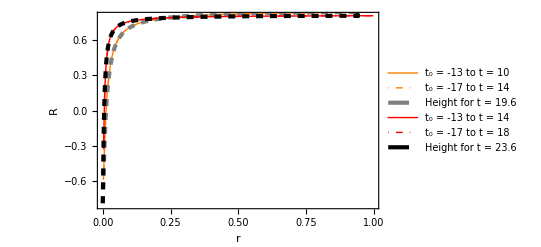
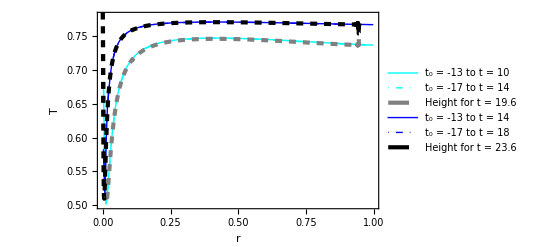
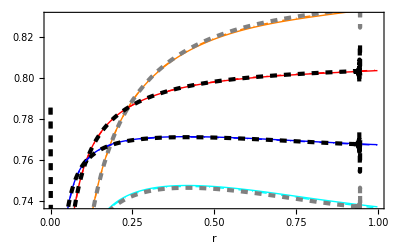

```mathematica
{Show[{ListLinePlot[{Rm[[4,11,2]],Rm[[8,15,2]]},PlotRange->All,PlotStyle->{{Orange,AbsoluteThickness[1]},{Orange,DotDashed,AbsoluteThickness[1]}}],Plot[ Rsall[19.6,r],{r,0,0.945},PlotStyle->{Gray,Dashed,AbsoluteThickness[3]},PlotRange->All],ListLinePlot[{Rm[[4,15,2]],Rm[[8,19,2]]},PlotRange->All,PlotStyle->{{Red,AbsoluteThickness[1]},{Red,DotDashed,AbsoluteThickness[1]}}],Plot[ Rsall[23.6,r],{r,0,0.945},PlotStyle->{Black,Dashed,AbsoluteThickness[3]},PlotRange->All]},PlotRange->{-0.8,0.8},ImageSize->400,Frame->True]//Quiet,Show[{ListLinePlot[{Tm[[4,11,2]],Tm[[8,15,2]]},PlotRange->All,PlotStyle->{{Cyan,AbsoluteThickness[1]},{Cyan,DotDashed,AbsoluteThickness[1]}}],Plot[ Tsall[19.6,r],{r,0,0.945},PlotStyle->{Gray,Dashed,AbsoluteThickness[3]},PlotRange->All],ListLinePlot[{Tm[[4,15,2]],Tm[[8,19,2]]},PlotRange->All,PlotStyle->{{Blue,AbsoluteThickness[1]},{Blue,DotDashed,AbsoluteThickness[1]}}],Plot[ Tsall[23.6,r],{r,0,0.945},PlotStyle->{Black,Dashed,AbsoluteThickness[3]},PlotRange->All]},PlotRange->{0.5,0.78},ImageSize->400,Frame->True]//Quiet};
{Show[{%[[1]],ListLinePlot[{{0,0}},PlotStyle->White,PlotLegends->Placed[Rlegend,{Scaled[{0.07,0}],{0,0}}]]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameLabel->{"r","R"},FrameStyle->Black,BaseStyle->{FontSize->14}],Show[{%[[2]],ListLinePlot[{{0,0}},PlotStyle->White,PlotLegends->Placed[Tlegend,{Scaled[{0.07,0}],{0,0}}]]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameLabel->{"r","T"},FrameStyle->Black,BaseStyle->{FontSize->14}(*,PlotLegends->Placed[Rlegend,Above]*)],Show[%,PlotRange->{0.738,0.83},ImageSize->400,Frame->True,BaseStyle->{FontColor->Black,FontSize->14,FontFamily->"Times"},FrameLabel->{"r",""},FrameStyle->Black,BaseStyle->{FontSize->15}(*,PlotLegends->Placed[Rlegend,Above]*)]}
```

```mathematica
(*(*for plotting last bit above for c=1*)Show[%,PlotRange->{{0.7,1},{0.738,0.83}},AspectRatio->4,ImageSize->55,Frame->True,BaseStyle->{FontColor->Black,FontSize->14,FontFamily->"Times"},FrameLabel->{"r",""},FrameStyle->Black,BaseStyle->{FontSize->15},FrameTicks->{{Automatic,Automatic},{{0.8,1},{0.8,1}}},ImagePadding->{{1,1},{46,1}}]*)
```

```mathematica
Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/Rcompar.pdf",%[[1]],"PDF"]
Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/Tcompar.pdf",%%[[2]],"PDF"]
Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/RTcompar.pdf",%%%[[3]],"PDF"]
```

/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/Rcompar.pdf

/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/Tcompar.pdf

/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/RTcompar.pdf

#### Comparison between height-function calculated (using Δh + f height function integration) and eikonal evolved non-CMC stationary data

```mathematica
(*construct R and T for the height function integrated using Δh and express them in terms of the compactified radial coordinate for ease of comparison*)
thsnum= {tphysKS -> t+dhccomp[r]};
Rsall=Compile[{t,r},(Rs/. thsnum/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc//Evaluate)//Evaluate];
Tsall=Compile[{t,r},(Ts/. thsnum/.mass->massset/.rphys->r/aconf[r]/.aconf->aconfc//Evaluate)//Evaluate];
```

```mathematica
legendtext=Flatten[{Map[MaTeX[#,Magnification->1.2]&,{"t_0=-13 \\textrm{ to } t=10","t_0=-17 \\textrm{ to } t = 14", "\\textrm{Height for }t = 43.9"}],Map[MaTeX[#,Magnification->1.14]&,{"t_0=-13 \\textrm{ to } t=14","t_0=-17 \\textrm{ to } t = 18", "\\textrm{Height for }t = 47.9"}]},1];
Rlegend=LineLegend[{Directive[Orange,AbsoluteThickness[1]],Directive[Orange,DotDashed,AbsoluteThickness[1]],Directive[Gray,Dashed,AbsoluteThickness[3]],Directive[Red,AbsoluteThickness[1]],Directive[Red,DotDashed,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[3]]},legendtext,LegendLayout->{"Column",2},LegendMarkerSize->22]
Tlegend=LineLegend[{Directive[Cyan,AbsoluteThickness[1]],Directive[Cyan,DotDashed,AbsoluteThickness[1]],Directive[Gray,Dashed,AbsoluteThickness[3]],Directive[Blue,AbsoluteThickness[1]],Directive[Blue,DotDashed,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[3]]},legendtext,LegendLayout->{"Column",2},LegendMarkerSize->22]
```

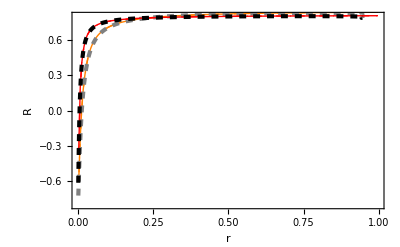
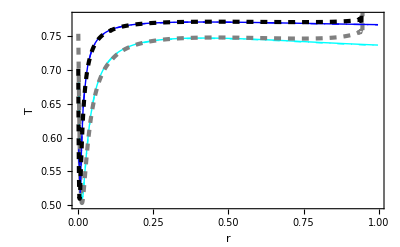
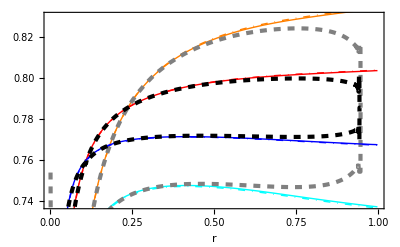

```mathematica
ibrad=0.001;obrad=0.946;addextra=0(*0.6*);
{Show[{ListLinePlot[{Rm[[4,11,2]],Rm[[8,15,2]]},PlotRange->All,PlotStyle->{{Orange,AbsoluteThickness[1]},{Orange,DotDashed,AbsoluteThickness[1]}}],Plot[ Rsall[43.9+addextra,r],{r,ibrad,obrad},PlotStyle->{Gray,Dashed,AbsoluteThickness[3]},PlotRange->All],ListLinePlot[{Rm[[4,15,2]],Rm[[8,19,2]]},PlotRange->All,PlotStyle->{{Red,AbsoluteThickness[1]},{Red,DotDashed,AbsoluteThickness[1]}}],Plot[ Rsall[47.9+addextra,r],{r,ibrad,obrad},PlotStyle->{Black,Dashed,AbsoluteThickness[3]},PlotRange->All]},PlotRange->{-0.8,0.8},ImageSize->400,Frame->True]//Quiet,Show[{ListLinePlot[{Tm[[4,11,2]],Tm[[8,15,2]]},PlotRange->All,PlotStyle->{{Cyan,AbsoluteThickness[1]},{Cyan,DotDashed,AbsoluteThickness[1]}}],Plot[ Tsall[43.9+addextra,r],{r,ibrad,obrad},PlotStyle->{Gray,Dashed,AbsoluteThickness[3]},PlotRange->All],ListLinePlot[{Tm[[4,15,2]],Tm[[8,19,2]]},PlotRange->All,PlotStyle->{{Blue,AbsoluteThickness[1]},{Blue,DotDashed,AbsoluteThickness[1]}}],Plot[ Tsall[47.9+addextra,r],{r,ibrad,obrad},PlotStyle->{Black,Dashed,AbsoluteThickness[3]},PlotRange->All]},PlotRange->{0.5,0.78},ImageSize->400,Frame->True]//Quiet};
{Show[{%[[1]],ListLinePlot[{{0,0}},PlotStyle->White,PlotLegends->Placed[Rlegend,{Scaled[{0.07,0}],{0,0}}]]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameLabel->{"r","R"},FrameStyle->Black,BaseStyle->{FontSize->14}],Show[{%[[2]],ListLinePlot[{{0,0}},PlotStyle->White,PlotLegends->Placed[Tlegend,{Scaled[{0.07,0}],{0,0}}]]},BaseStyle->{FontColor->Black,FontSize->15,FontFamily->"Times"},FrameLabel->{"r","T"},FrameStyle->Black,BaseStyle->{FontSize->14}(*,PlotLegends->Placed[Rlegend,Above]*)],Show[%,PlotRange->{0.738,0.83},ImageSize->400,Frame->True,BaseStyle->{FontColor->Black,FontSize->14,FontFamily->"Times"},FrameLabel->{"r",""},FrameStyle->Black,BaseStyle->{FontSize->15}(*,PlotLegends->Placed[Rlegend,Above]*)]}
```

```mathematica
(*(*for plotting last bit above for c=1*)Show[%[[3]],PlotRange->{{0.7,1},{0.738,0.83}},AspectRatio->4,ImageSize->55,Frame->True,BaseStyle->{FontColor->Black,FontSize->14,FontFamily->"Times"},FrameLabel->{"r",""},FrameStyle->Black,BaseStyle->{FontSize->15},FrameTicks->{{Automatic,Automatic},{{0.8,1},{0.8,1}}},ImagePadding->{{1,1},{46,1}}]*)
```

```mathematica
(*Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/Rcompar.pdf",%[[1]],"PDF"]
Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/Tcompar.pdf",%%[[2]],"PDF"]
Export["/home/alex/darkchest/postdoc_lisboa/articles/penrose/figures/RTcompar.pdf",%%%[[3]],"PDF"]*)
```

## Collapse

### Load data

```mathematica
(*initial data start from a Minkowski CMC slice*)
{repolocation<>"HypPenroseDiagrams/data/pentrevolm4new_diag_R_c4_single.yg",repolocation<>"HypPenroseDiagrams/data/pentrevolm4new_diag_T_c4_single.yg"};
vard=Map[{ReadPygraph[#]}&,%];
diagdatam4new=Table[{vard[[1,1,ct,1]],Table[{vard[[1,1,ct,2,st,2]]/2,vard[[2,1,ct,2,st,2]]/2},{st,1,Length@vard[[1,1,ct,2]]}]},{ct,1,Length@vard[[1,1]]}];
{repolocation<>"HypPenroseDiagrams/data/pentrevolm5new_diag_R_c4_single.yg",repolocation<>"HypPenroseDiagrams/data/pentrevolm5new_diag_T_c4_single.yg"};
vard=Map[{ReadPygraph[#]}&,%];
diagdatam5new=Table[{vard[[1,1,ct,1]],Table[{vard[[1,1,ct,2,st,2]]/2,vard[[2,1,ct,2,st,2]]/2},{st,1,Length@vard[[1,1,ct,2]]}]},{ct,1,Length@vard[[1,1]]}];
```

read 5186.95 KByte of data;

read 5101.63 KByte of data;

read 5031.3 KByte of data;

read 5137.98 KByte of data;

```mathematica
(*initial data start from a perturbed Minkowski slice*)
{repolocation<>"HypPenroseDiagrams/data/pentrevolm07_diag_R_c4_single.yg",repolocation<>"HypPenroseDiagrams/data/pentrevolm07_diag_T_c4_single.yg"};
vard=Map[{ReadPygraph[#]}&,%];
diagdatam07pert=Table[{vard[[1,1,ct,1]],Table[{vard[[1,1,ct,2,st,2]],vard[[2,1,ct,2,st,2]]},{st,1,Length@vard[[1,1,ct,2]]}]},{ct,1,Length@vard[[1,1]]}];
{repolocation<>"HypPenroseDiagrams/data/pentrevol0_diag_R_c4_single.yg",repolocation<>"HypPenroseDiagrams/data/pentrevol0_diag_T_c4_single.yg"};
vard=Map[{ReadPygraph[#]}&,%];
diagdata0pert=Table[{vard[[1,1,ct,1]],Table[{vard[[1,1,ct,2,st,2]],vard[[2,1,ct,2,st,2]]},{st,1,Length@vard[[1,1,ct,2]]}]},{ct,1,Length@vard[[1,1]]}];
```

read 5211.34 KByte of data;

read 5274.8 KByte of data;

read 5243.53 KByte of data;

read 5218.06 KByte of data;

### Static plots

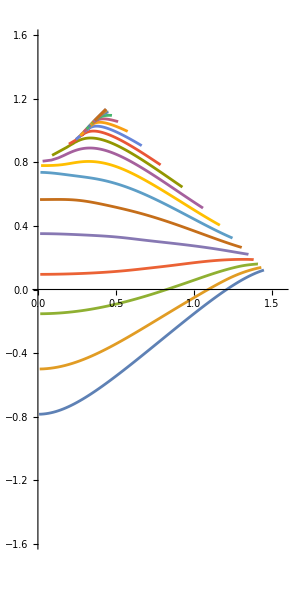
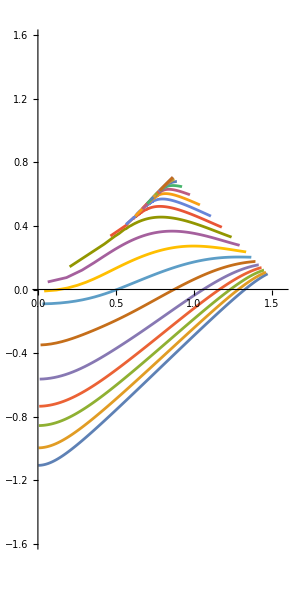
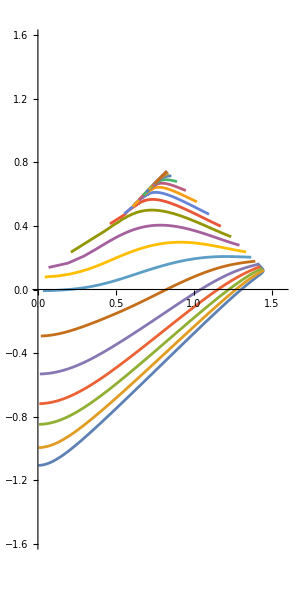
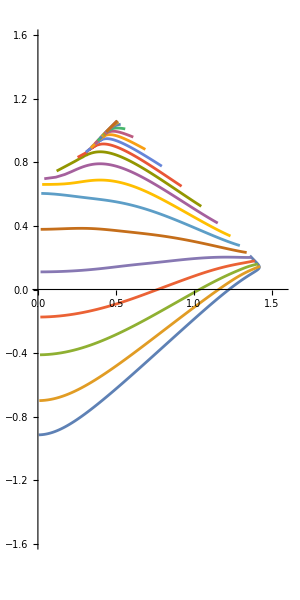

```mathematica
{ListLinePlot[diagdatam4new[[;;;;5,2]],PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2,ImageSize->300],ListLinePlot[diagdatam5new[[;;;;5,2]],PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2,ImageSize->300],ListLinePlot[diagdatam07pert[[;;;;5,2]],PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2,ImageSize->300],ListLinePlot[diagdata0pert[[;;;;5,2]],PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2,ImageSize->300]}//Quiet
```

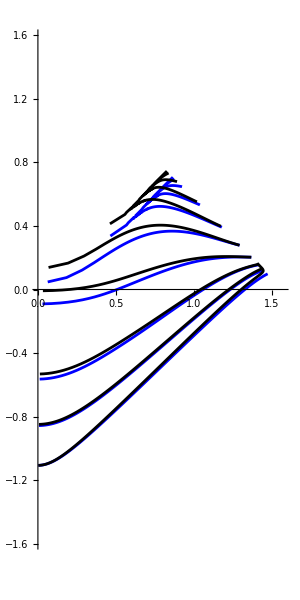

```mathematica
(*comparison between initially CMC and perturbed slices*)
{ListLinePlot[diagdatam5new[[;;;;10,2]],PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2,ImageSize->300,PlotStyle->Blue],ListLinePlot[diagdatam07pert[[;;;;10,2]],PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2,ImageSize->300,PlotStyle->Black]}//Quiet;
Show[%[[1]],%[[2]]]
```

```mathematica
(*initial data start from a perturbed Minkowski slice*)
{Show[letterscol[0.55],
covercol[0.55],ListLinePlot[diagdata0pert[[;;;;5,2]],PlotRange->{{-π/2,π/2},{-π/2,π/2}}],ImageSize->350],Show[
letterscol[-0.08],covercol[-0.08],ListLinePlot[diagdatam07pert[[;;;;5,2]],PlotRange->{{-π/2,π/2},{-π/2,π/2}}],ImageSize->350]}//Quiet
```

{-Graphics-,-Graphics-}

```mathematica
(*initial data start from a Minkowski CMC slice*)
{Show[letterscol[0.7],
covercol[0.7],ListLinePlot[diagdatam4new[[;;;;5,2]],PlotRange->{{-π/2,π/2},{-π/2,π/2}}(*,PlotStyle->{{Thick, Dashed}}*)],ImageSize->350(*{Automatic,500}*)],Show[
letterscol[-0.15],covercol[-0.15],ListLinePlot[diagdatam5new[[;;;;5,2]],PlotRange->{{-π/2,π/2},{-π/2,π/2}}(*,PlotStyle->{{Thick, Dashed}}*)](*,PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2*),ImageSize->350(*{Automatic,500}*)]}//Quiet
```

{-Graphics-,-Graphics-}

### Evolution plots

```mathematica
colframes=Table[Show[
letterscol[-0.15],covercol[-0.15],ListLinePlot[diagdatam5new[[ti,2]],PlotRange->{{-π/2,π/2},{-π/2,π/2}},PlotStyle->{{Thick}}](*,PlotRange->{{0,π/2},{-π/2,π/2}},AspectRatio->2*),ImageSize->{Automatic,500}],{ti,1,Length@diagdatam5new}]//Quiet;
```

```mathematica
ListAnimate[colframes,AnimationRunning->False]
```

```mathematica
Export[repolocation<>"HypPenroseDiagrams/gifs/colm5.gif",colframes,"DisplayDurations"->0.1]
```

~/other_repos/paper_repos/HypPenroseDiagrams/gifs/colm5.gif

```mathematica
(*to export each frame as png image -- suitable for use with LaTeX beamer's animate package*)
(*Export[repolocation<>"HypPenroseDiagrams/gifs/colm5_000.png",colframes,"VideoFrames"]*)
```

## Appendix A -- translating metric quantities from conformally compactified domain to physical one

#### Analytical example for lapse

```mathematica
(*lapse can be done analytically*)
αb[r]/Ω[r]/.trumpetsubsb/.Q->0(*expression for physical domain quantity expressed in terms of quantities in the conformally compactified domain*)
Simplify[%/.aconf[r]->aconf/.r->rp aconf,Assumptions->{rp∈Reals,rp>0,aconf∈Reals, aconf>0}]
αb[rp]/.trumpetunco(*expression for physical domain quantity in the physical domain*)
(%%)^2-%^2//Simplify
```

(√(Kcmc^2 r^6+9 r^4 aconf[r]^2+6 (Ccmc Kcmc-3 mass) r^3 aconf[r]^3+9 Ccmc^2 aconf[r]^6))/(3 r^2 aconf[r])

(√(9 Ccmc^2+6 Ccmc Kcmc rp^3+rp^3 (-18 mass+9 rp+Kcmc^2 rp^3)))/(3 rp^2)

1/3 √(9+(9 Ccmc^2)/rp^4+(6 Ccmc Kcmc)/rp-(18 mass)/rp+Kcmc^2 rp^2)

0

#### Numerical transformations

```mathematica
(*to express the compactified radial coordinate in terms of the non-compactified physical one*)
delt=0.01(*0.001*);
rofrphys=Interpolation[Map[{r/(Ω[r]Sqrt[χc[r]Sqrt[grrc[r]]]/.omega/.Kcmc->Kcmcset/.rscri->1/.subaconf),r}/.r->#&,Range[0+(*3*)delt,1-delt,delt]]]
Plot[rofrphys[rphys],{rphys,inmstR,10}]
```

InterpolatingFunction[…]

-Graphics-

Curves in the left plots in the following cells will only coincide if CMC data is used.

```mathematica
αc[r]/Ω[r]//Simplify;
%/.omega/.Kcmc->Kcmcset/.rscri->1/.subaconf/.schwsubs;
αp[rphys_]=%/.r->rofrphys[rphys];
αb[rp]/.trumpetunco
{Plot[{(%/.rp->rphys/.schwsubs),%%},{rphys,inmstR,10},ImageSize->400],Plot[{(%/.rp->rphys/.schwsubs)-%%},{rphys,inmstR,10},ImageSize->400]}
```

1/3 √(9+(9 Ccmc^2)/rp^4+(6 Ccmc Kcmc)/rp-(18 mass)/rp+Kcmc^2 rp^2)

{-Graphics-,-Graphics-}

```mathematica
χc[r]Ω[r]^2/aconf[r]^2/.aconf->Function[{r},Ω[r]Sqrt[χc[r]Sqrt[grrc[r]]]]//Simplify;
%/.omega/.Kcmc->Kcmcset/.rscri->1/.subaconf/.schwsubs;
χp[rphys_]=%/.r->rofrphys[rphys];
χb[rp]/.trumpetunco
{Plot[{(%/.rp->rphys/.schwsubs),%%},{rphys,inmstR,10},ImageSize->400],Plot[{(%/.rp->rphys/.schwsubs)-%%},{rphys,inmstR,10},ImageSize->400]}
```

1

{-Graphics-,-Graphics-}

```mathematica
grrc[r](aconf[r]/(aconf[r]-r aconf'[r]))^2/.aconf->Function[{r},Ω[r]Sqrt[χc[r]Sqrt[grrc[r]]]]//Simplify;
%/.omega/.Kcmc->Kcmcset/.rscri->1/.subaconf;
grrp[rphys_]=%/.r->rofrphys[rphys];
grrb[rp]/.trumpetunco
{Plot[{(%/.rp->rphys/.schwsubs),%%},{rphys,inmstR,10},ImageSize->400],Plot[{(%/.rp->rphys/.schwsubs)-%%},{rphys,inmstR,10},ImageSize->400]}
```

(9 rp^4)/(9 Ccmc^2+6 Ccmc Kcmc rp^3+rp^3 (-18 mass+9 rp+Kcmc^2 rp^3))

{-Graphics-,-Graphics-}

```mathematica
βrc[r](aconf[r]-r aconf'[r])/aconf[r]^2/.aconf->Function[{r},Ω[r]Sqrt[χc[r]Sqrt[grrc[r]]]]//Simplify;
%/.omega/.Kcmc->Kcmcset/.rscri->1/.subaconf/.schwsubs;
βrp[rphys_]=%/.r->rofrphys[rphys];
βrb[rp]/.trumpetunco
{Plot[{(%/.rp->rphys/.schwsubs),%%},{rphys,inmstR,10},ImageSize->400],Plot[{(%/.rp->rphys/.schwsubs)-%%},{rphys,inmstR,10},ImageSize->400]}
```

((3 Ccmc+Kcmc rp^3) √(9 Ccmc^2+6 Ccmc Kcmc rp^3+rp^3 (-18 mass+9 rp+Kcmc^2 rp^3)))/(9 rp^4)

{-Graphics-,-Graphics-}

#### Check using relations valid in the stationary regime

```mathematica
(*in the compactified domain on the left and the physical one on the right: curves have to be very close to zero*)
{grrc[r]/χc[r]-(c/αc[r]Ω[r]^2/aconfc[r]^2(aconfc[r]-r aconfc'[r]))^2,αc[r]^2-βrc[r]^2 grrc[r]/χc[r]-(c^2 Ω[r]^2(1-2mass aconfc[r]/r))}//.schwsubs;
{grrp[rphys]/χp[rphys]-(c^2/αp[rphys]^2),αp[rphys]^2-βrp[rphys]^2 grrp[rphys]/χp[rphys]-(c^2(1-2mass/rphys))}//.schwsubs;
{Plot[%%,{r,0,1},ImageSize->400],Plot[%,{rphys,inmstSchwrad,5},ImageSize->400]}//Quiet
```

{-Graphics-,-Graphics-}